# AMASeriesRepresentation Examples

## Model Component Validation

### getB, getF, getPhi, genx0z0Funcs, genX0Z0Funcs,checkLinMod,, checkMod

```mathematica
?getB
```

getB[linMod] B from linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ}

```mathematica
?getF
```

getF[linMod] F from linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ}

```mathematica
?getPhi
```

getPhi[linMod] Phi from linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ}

```mathematica
Through[{getB,getF,getPhi}[notLinMod]]
```

{{{-0.0282384,-0.0552487,0.00939369},{-0.0664679,-0.700462,-0.0718527},{-0.163638,-1.39868,0.331726}},{{-0.381174,-0.223904,0.0940684},{-0.134352,-0.189653,0.630956},{-0.816814,-1.00033,0.0417094}},{{0.0210079,0.15727,-0.0531634},{1.20712,-0.0553003,-0.431842},{2.58165,-0.183521,-0.578227}}}

```mathematica
?genx0z0Funcs
```

genX0Z0Funcs[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ}]
returns functions x0(xtm1,eps) and z0(xtm1,eps)  based on the linear reference model

```mathematica
x0z0func=genx0z0Funcs[linMod] ;x0z0func @@ anXEpsFlat
```

{{0.392799},{0.20416},{1.10505},{0},{0},{0}}

```mathematica
?genX0Z0Funcs
```

genX0Z0Funcs[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ}]
returns functions  expected X0(xtm1) and Z0(xtm1)   based on the linear reference model

```mathematica
X0Z0func=genX0Z0Funcs[linMod];X0Z0func @@ anXFlat
```

{{0.389195},{0.202287},{1.09505},{0},{0},{0}}

```mathematica
?checkLinMod
```

checkLinMod[linMod,anX_?MatrixQ,anEps_?MatrixQ,numRegimes_Integer:0]
computes eigenvalues and checks consistency of dimensions of model components
returns {Eigenvalues[BB]//Abs,Eigenvalues[FF]//Abs,X0Z0 @@anX,lilxz @@Join[anX,anEps,Table[0,{numZ}]]}
numRegimes currently has no impact

```mathematica
checkLinMod[linMod,anX,anEps]
```

{{0.949953,0.36,0.},{0.342,0.,0.},{{0.389195},{0.202287},{1.09505},{0},{0},{0}},{{0.2},{0.18},{1.1},{0.392799},{0.20416},{1.10505},{0.407658},{0.211883},{1.09985},{0.01}}}

```mathematica
?checkMod
```

checkMod[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
gSpec:{toIgnore:{_Integer...},iOrd_Integer,{{_Integer,_?NumberQ,_?NumberQ}..},numRegimes_:0},
distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},anX_?MatrixQ,anEps_?MatrixQ,
eqnsFunc:(_Function|_CompiledFunction)]

```mathematica
checkMod[linMod,aGSpec,theDist,anX,{{0.7}},rbcEqnsFunctionalNext]
```

{{{0.2},{0.18},{1.1},{0.641468},{0.333407},{1.79571},{0.733403},{0.381191},{1.75594},{0.7}},{{0.754557},{0.434568},{2.2046},{0.627752},{-0.00948746},{0.408886}},{{0.754557},{0.434568},{2.2046},{0.627752},{-0.00948746},{0.408886}}}

### truncErrorMat

```mathematica
?truncErrorMat
```

truncErrorMat[{{fmat,_Real,2},{phimat,_Real,2},{kk,_Integer}}]

computes the truncation error matrix

```mathematica
truncErrorMat[getF[notLinMod],getPhi[notLinMod],3]
```

{{0.246116,-0.0114312,-0.0661884},{-0.00370631,0.058752,-0.0692077},{1.08452,-0.0635452,-0.272294}}

## Construct AMA Series Given a Solution Path or Given a Decision Rule (Both Perfect Foresight and Rational Expectations)

### genZsFromPath

```mathematica
?genZsFromPath
```

genZsFromPath[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
thePath_?MatrixQ,theEps_?MatrixQ]

    given the path
	computes the z values using the hmat in linMod
	returns a list of z matrices(one column matrices)

```mathematica
iterateDRREIntegrate[simpRBCExactDR,anXEps,theDist,6]
```

{{0.2},{0.18},{1.1},{0.392455},{0.203981},{1.10577},{0.408491},{0.212316},{1.10028},{0.412468},{0.214383},{1.09509},{0.412055},{0.214168},{1.09018},{0.410152},{0.213179},{1.08554},{0.407812},{0.211963},{1.08115}}

```mathematica
sip=genZsFromPath[linMod,iterateDRREIntegrate[simpRBCExactDR,anXEps,theDist,6],anXEps[[{-1}]]]
```

{{{0.00615901},{-0.000915881},{0.000718209}},{{0.00671986},{0.00121583},{-0.000246413}},{{0.00611557},{0.00132655},{-0.000221425}},{{0.00548079},{0.00120726},{-0.000198992}},{{0.00491736},{0.00108195},{-0.000178848}}}

### iterateDRREIntegrate

```mathematica
?iterateDRREIntegrate
```

iterateDRREIntegrate[drFunc:(_Function|_CompiledFunction),initVec_?MatrixQ,
	distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},numPers_Integer]
	
Iterates a decision rule forward from initVec(includes time zero shocks) for numPers time intervals by integrating out the shocks 
using the distribution
and, if not {},the regime change transition probablities

produces a matrix containing the path

```mathematica
kip=iterateDRREIntegrate[simpRBCExactDR,anXEps,theDist,2]
```

{{0.2},{0.18},{1.1},{0.392455},{0.203981},{1.10577},{0.408491},{0.212316},{1.10028}}

```mathematica
kip=iterateDRREIntegrate[simpRBCExactDR,anXEps,theDist,5]
```

{{0.2},{0.18},{1.1},{0.392455},{0.203981},{1.10577},{0.408491},{0.212316},{1.10028},{0.412468},{0.214383},{1.09509},{0.412055},{0.214168},{1.09018},{0.410152},{0.213179},{1.08554}}

### genZsREExact

```mathematica
?genZsREExact
```

genZsREExact[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
	initVec_?MatrixQ,distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},theExactDR:(_Function|_CompiledFunction),iters_Integer]
	
	iterates a decision rule forward using iterateDRIntegrate (can use PerfectForesight as distribution for specific shocks)
	computes the z values using the hmat in linMod
	returns a list of z matrices(one column matrices)

```mathematica
rip=genZsREExact[linMod,anXEps,theDist,simpRBCExactDR,5]
```

{{{0.00615901},{-0.000915881},{0.000718209}},{{0.00671986},{0.00121583},{-0.000246413}},{{0.00611557},{0.00132655},{-0.000221425}},{{0.00548079},{0.00120726},{-0.000198992}},{{0.00491736},{0.00108195},{-0.000178848}}}

### genASeriesRep

```mathematica
?genASeriesRep
```

genASeriesRep[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
	initVec_?MatrixQ,theZs:{_?MatrixQ..},len_Integer]
	
matrix of the  values for {xtm1,xt,xtp1,eps} from the series representations using 
from the first len z matrices

```mathematica
rip=genZsREExact[linMod,anXEps,theDist,simpRBCExactDR,5];trySer=genASeriesRep[linMod,anXEps,rip,5]
```

{{0.2},{0.18},{1.1},{0.391974},{0.204462},{1.10577},{0.407766},{0.211944},{1.10125},{0.01}}

```mathematica
sip=genZsFromPath[linMod,iterateDRREIntegrate[simpRBCExactDR,anXEps,theDist,6],anXEps[[{-1}]]];
trySer=genASeriesRep[linMod,anXEps,sip,5]
```

{{0.2},{0.18},{1.1},{0.391974},{0.204462},{1.10577},{0.407766},{0.211944},{1.10125},{0.01}}

```mathematica
sip
```

{{{0.00615901},{-0.000915881},{0.000718209}},{{0.00671986},{0.00121583},{-0.000246413}},{{0.00611557},{0.00132655},{-0.000221425}},{{0.00548079},{0.00120726},{-0.000198992}},{{0.00491736},{0.00108195},{-0.000178848}}}

### genSeriesReps

```mathematica
?genSeriesReps
```

genSeriesReps[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
initVec_?MatrixQ,distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},theExactDR:(_Function|_CompiledFunction),maxIters_Integer]
	
generates  Zs using genZsREExact, then uses genASeriesRep to generate a list of the possible  values for {xtm1,xt,xtp1,eps} from the series representations using 
from just the first z matrix to all the z's

```mathematica
arbMod=genSeriesReps[linMod,anXEps,theDist,simpRBCExactDR,5]
```

{{{0.2},{0.18},{1.1},{0.391974},{0.204462},{1.10577},{0.407766},{0.211944},{1.10125},{0.01}},{{0.2},{0.18},{1.1},{0.391974},{0.204462},{1.10577},{0.407766},{0.211944},{1.10125},{0.01}},{{0.2},{0.18},{1.1},{0.391974},{0.204462},{1.10577},{0.407766},{0.211944},{1.10125},{0.01}},{{0.2},{0.18},{1.1},{0.391974},{0.204462},{1.10577},{0.407766},{0.211944},{1.10125},{0.01}},{{0.2},{0.18},{1.1},{0.391974},{0.204462},{1.10577},{0.407766},{0.211944},{1.10125},{0.01}}}

### genSeriesRepFunc

```mathematica
?genSeriesRepFunc
```

genSeriesRepFunc[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},theExactDR:(_Function|_CompiledFunction),terms_Integer]
	
generates  Zs using genZsREExact, then 
returns a function that 
uses genASeriesRep to generate the value for  {xtm1,xt,xtp1,eps} from the the series representation with the given number of terms

```mathematica
arbModFunc=genSeriesRepFunc[linMod,theDist,simpRBCExactDR,5];
arbModFunc@@anXEps
```

{{0.2},{0.18},{1.1},{0.391974},{0.204462},{1.10577},{0.407766},{0.211944},{1.10125},{0.01}}

## Evaluate Solution Path Errors

### evalPathErrDRREIntegrate

```mathematica
?evalPathErrDRREIntegrate
```

evalPathErrDRREIntegrate[drFunc_Function,initVec_?MatrixQ,distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},eqnsFunc:(_Function|_CompiledFunction)]

uses decision rule to compute an unconditional expectations path of length 2, then applies eqnsFunc 
returns a  vector of equations errors

```mathematica
evalPathErrDRREIntegrate[simpRBCExactDR,anXEps,theDist,rbcEqnsFunctionalNext]
```

{{0.},{1.11022×10^-16},{0.}}

```mathematica
evalPathErrDRREIntegrate[simpRBCExactDR,anXEps,theDist,rbcEqnsFunctionalNext]
```

{{0.},{1.11022×10^-16},{0.}}

### pathErrsDRREIntegrate

```mathematica
?pathErrsDRREIntegrate
```

pathErrsDRREIntegrate[drFunc_Function,initVec_?MatrixQ,distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},eqnsFunc:(_Function|_CompiledFunction),numPers_Integer]

uses decision rule to compute an unconditional expectations path of length numPers, then applies eqnsFunc along the path
returns List of vectors of equations errors

```mathematica
pathErrsDRREIntegrate[simpRBCExactDR,anXEps,theDist,rbcEqnsFunctionalNext,8]
```

{{{0.},{1.11022×10^-16},{0.}},{{1.33227×10^-15},{1.11022×10^-16},{0.0000550128}},{{-4.44089×10^-16},{4.44089×10^-16},{0.0000547533}},{{-4.44089×10^-16},{0.},{0.0000545079}},{{-8.88178×10^-16},{2.22045×10^-16},{0.0000542758}},{{-8.88178×10^-16},{-1.11022×10^-16},{0.0000540562}},{{0.},{-1.11022×10^-16},{0.0000538484}}}

```mathematica
pathErrsDRREIntegrate[simpRBCExactDR,anXEps,theDist,rbcEqnsFunctionalNext,8]
```

{{{0.},{1.11022×10^-16},{0.}},{{1.33227×10^-15},{1.11022×10^-16},{0.0000550128}},{{-4.44089×10^-16},{4.44089×10^-16},{0.0000547533}},{{-4.44089×10^-16},{0.},{0.0000545079}},{{-8.88178×10^-16},{2.22045×10^-16},{0.0000542758}},{{-8.88178×10^-16},{-1.11022×10^-16},{0.0000540562}},{{0.},{-1.11022×10^-16},{0.0000538484}}}

### evalBadPathErrDRREIntegrate

```mathematica
?evalBadPathErrDRREIntegrate
```

evalBadPathErrDRREIntegrate[drFunc_Function,noEpsVec_?MatrixQ,
distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},eqnsFunc:(_Function|_CompiledFunction)]

given the initial state vector and the decision rule uses FindMaximum to find the time t shock that produces the largest infinity norm for the error in the
system equations
returns the infintiy norm of the error and the shock value

```mathematica
evalBadPathErrDRREIntegrate[simpRBCExactDR,Drop[anXEps,-1],theDist,rbcEqnsFunctionalNext]
```

{4.44089×10^-16,{eVs101→0.}}

### worstPathForErrDRREIntegrate

```mathematica
?worstPathForErrDRREIntegrate
```

worstPathForErrDRREIntegrate[drFunc_Function,noEpsVec_?MatrixQ,distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},eqnsFunc:(_Function|_CompiledFunction)]

returns the path corresponding to evalBadPathErrDRREIntegrate

```mathematica
worstPathForErrDRREIntegrate[simpRBCExactDR,Drop[anXEps,-1],theDist,rbcEqnsFunctionalNext]
```

{{0.2},{0.18},{1.1},{0.38855},{0.201952},{1.09477},{0.403175},{0.209553},{1.08988},{0.}}

```mathematica
worstPathForErrDRREIntegrate[simpRBCExactDR,Drop[anXEps,-1],theDist,rbcEqnsFunctionalNext]
```

{{0.2},{0.18},{1.1},{0.38855},{0.201952},{1.09477},{0.403175},{0.209553},{1.08988},{0.}}

### genErrsREWorst

```mathematica
?genErrsREWorst
```

genErrsREWorst[theDRFunc:(_Function|_CompiledFunction),initVec_?MatrixQ,distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},
	theSysFunc:(_Function|_CompiledFunction),iters_Integer]
	
	iterates the decision rule using iterateDRREIntegrate
	applies worstPathForErrDRREIntegrate all along the path to return a list of
	vectors corresponding to maximum infinity norm errors in the sysFunc equations

```mathematica
genErrsREWorst[simpRBCExactDR,anXEps,theDist,rbcEqnsFunctionalNext,2]
```

done thePath

done worstPaths{{{0.392455},{0.203981},{1.10577},{0.408471},{0.212306},{1.10023},{0.412441},{0.214369},{1.09504},{-3.15386×10^-10}},{{0.408491},{0.212316},{1.10028},{0.412448},{0.214373},{1.09504},{0.412027},{0.214154},{1.09013},{-1.07052×10^-7}},{{0.412468},{0.214383},{1.09509},{0.412034},{0.214157},{1.09013},{0.410125},{0.213165},{1.08549},{-4.50526×10^-10}}}{1,2,3}

{{{1.33227×10^-15},{1.11022×10^-16},{0.}},{{2.22045×10^-15},{0.},{0.}},{{2.22045×10^-15},{1.11022×10^-16},{0.}}}

## Construct Solution Decision Rule Series Components

### makeDREvalInterp, doIterREInterp, nestIterREInterp

### makeDREvalInterp

```mathematica
?makeInterpFunc
```

makeInterpFunc[aVecFunc_Function,
gSpec:{toIgnore:{_Integer...},iOrd_Integer,{{_Integer,_?NumberQ,_?NumberQ}..},numRegimes_:0}]

returns an interpolating function based on the vector function and grid specification

```mathematica
tryFunc=Function[{ww,yy,zz,xx},{{Sin[xx]*yy*E^zz},{xx+yy/zz},{99*zz}}];huh=makeInterpFunc[tryFunc,aGSpec];huh[2,.2,1,.01]
```

{{0.00543949},{0.210222},{99.}}

```mathematica
?makeDREvalInterp
```

makeDREvalInterp[drFunc_Function,distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},
eqnsFunc:(_Function|_CompiledFunction),gSpec:{toIgnore:{_Integer...},iOrd_Integer,{{_Integer,_?NumberQ,_?NumberQ}..},numRegimes_:0}]

returns a list of two functions: the first evaluates the error in the equations without interpolation, the second uses interpolation

```mathematica
{ theNotInterp,theInterp}=makeDREvalInterp[simpRBCExactDR,theDist,rbcEqnsFunctionalNext,aGSpec];
```

```mathematica
{theInterp @@ anXEpsFlat,theNotInterp @@ anXEpsFlat}
```

{{{-4.96059×10^-16},{0.},{0.}},{{0.},{1.11022×10^-16},{0.}}}

### fSum, fSumC

```mathematica
?fSum
```

fSum[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
	{},
	xtGuess_?MatrixQ]

returns matrix of the F weigthed sum of z's

```mathematica
anX0Z0=genX0Z0Funcs[linMod];


{nxtxz,nxtXZ}=doIterREInterp[linMod,{anX0Z0,1},rbcEqnsFunctionalNext,aGSpec,theDist];
```

```mathematica
fSum[linMod,{nxtXZ,7},anX]
```

{{-0.0123996},{-0.00548627},{-0.0000749254}}

```mathematica
?fSumC
```

fSumC=Compile[{{phi,_Real,2},{FF,_Real,2},{psiZ,_Real,2},{zPath,_Real,3}},...]


returns matrix of the F weigthed sum of z's

```mathematica
rip=genZsREExact[linMod,anXEps,theDist,simpRBCExactDR,5];
fSumC[getB[linMod],getF[linMod],IdentityMatrix[3],rip]
```

{{0.000050454},{-0.000641214},{0.000682265}}

### compareFormula, genPathCompare

```mathematica
?compareFormula
```

compareFormula[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
	{XZFunc_Function,numSteps_Integer},xtm1Vars_?MatrixQ,epsVars_?MatrixQ,xtztVal_?MatrixQ]

```mathematica
compareFormula[linMod,{X0Z0func,5},anX,anEps,Drop[anXEpsZs,{4}]]
```

{{0.2},{0.18},{1.1},{0.627971},{0.333144},{1.40505},{0.599605},{0.311649},{1.38483},{0.01}}

### genLilXkZkFunc

```mathematica
?genLilXkZkFunc
```

genLilXkZkFunc[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
	XZFuncs:({_Function,_Integer}),xtGuess_?MatrixQ]

uses the guess to compute the F sum in AMA series expansion
returns a function	(xtm1,eps,zvars) that returns a vector of{xtm1,xt,xtp1,eps) values

```mathematica
anX0Z0=genX0Z0Funcs[linMod];
lilxkzk=genLilXkZkFunc[linMod,{anX0Z0,3},anX0Z0@@ anXEpsFlat];
```

```mathematica
lilxkzk@@ anXEpsZsFlat
```

{{0.2},{0.18},{1.1},{0.627971},{0.333144},{1.40505},{0.599605},{0.311649},{1.38483},{0.01}}

```mathematica
With[{better=Flatten[nxtxz @@ anXEpsZsFlat]},{lilxkzk @@ anXEpsZsFlat,better,lilxkzk @@ Flatten[Join[better[[{1,2,3}]],anEps,better[[{4,5,6}]]]]}]
```

{{{0.2},{0.18},{1.1},{0.627971},{0.333144},{1.40505},{0.599605},{0.311649},{1.38483},{0.01}},{0.381458,0.197797,1.10577,-0.00692871,-0.018097,0.000718209},{{0.381458},{0.197797},{1.10577},{0.395759},{0.205231},{1.11126},{0.410521},{0.213371},{1.10574},{0.01}}}

### genFRFunc

```mathematica
?genFRFunc
```

genFRFunc[{numX_Integer,numEps_Integer,numZ_Integer},
xkFunc:(_Function|_CompiledFunction),eqnsFunc:(_Function|_CompiledFunction)]

returns a function that uses FindRoot to solve the eqnsFunc system using the xkFuncs in the series approximation for the conditional expectations function

```mathematica
anX0Z0=genX0Z0Funcs[linMod];
lilxkzk=genLilXkZkFunc[linMod,{anX0Z0,1},anX0Z0@@ anXEpsFlat];
frf=genFRFunc[{3,1,3},lilxkzk,rbcEqnsFunctionalNext];
frf @@ anXEpsFlat
```

{{0.392189},{0.204248},{1.10577},{0.00599681},{-0.000915881},{0.000718209}}

### genFPFunc

```mathematica
?genFPFunc
```

genFPFunc[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
XZFuncs:({_Function,_Integer}),eqnsFunc:(_Function|_CompiledFunction)]

returns a function (xtm1,eps) by  iterating  to get  the correct value of xt (zt) to use in the conditional expectations function and iterates until the guess is consitent with the root finding solution

```mathematica
anX0Z0=genX0Z0Funcs[linMod];
lilxkzk=genLilXkZkFunc[linMod,{anX0Z0,2},anX0Z0@@anXEpsFlat];
anX0Z0=genX0Z0Funcs[linMod];
{nxtxz,nxtXZ}=doIterREInterp[linMod,{anX0Z0,2},rbcEqnsFunctionalNext,aGSpec,theDist];
thisOne=genXZFuncREInterp[{3,1,3},nxtxz,aGSpec,theDist];
```

```mathematica
fpf=genFPFunc[linMod,{thisOne,2},rbcEqnsFunctionalNext];
fpf @@ anXEpsFlat
```

InterpolatingFunction::dmval: Input value {0.205154,1.10577} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{0.392135},{0.204301},{1.10577},{0.00595345},{-0.000915881},{0.000718209}}

```mathematica
thisOne  @@ anXFlat
```

{{0.37777},{0.195827},{1.09497},{-0.00772797},{-0.0178449},{-0.0000749254}}

```mathematica
?genPathCompare
```

genPathCompare[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
	xzFunc_Function,{XZFunc_Function,numSteps_Integer},xtm1Val_?MatrixQ,epsVal_?MatrixQ]

```mathematica
genPathCompare[linMod,x0z0func,{X0Z0func,1},anX,anEps]
```

{{{0.2},{0.18},{1.1},{0.407658},{0.211883},{1.09985},{0.411226},{0.213738},{1.0949}},{{0.2},{0.18},{1.1},{0.392799},{0.20416},{1.10505},{0.407658},{0.211883},{1.09985},{0.01}}}

```mathematica
?doIterREInterp
```

doIterREInterp[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
	XZFuncsNow:{(_Function|_InterpolatingFunction|_CompiledFunction),_Integer},
eqnsFunc:(_Function|_CompiledFunction),gSpec:{toIgnore:{_Integer...},iOrd_Integer,{{_Integer,_?NumberQ,_?NumberQ}..},numRegimes_:0},distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}}]




given a reference linear model, (x,z,X,Z) function and  and equation system
extends (x,z,X,Z) an additional period imposing rational expectations using interpolation to avoid recalculation of all the points along the path

returns a pair of functions xz and XZ giving the xt values of x and z and giving the unconditional expected path of future values of x and z

```mathematica
{nxtxz,nxtXZ}=doIterREInterp[linMod,{anX0Z0,2},rbcEqnsFunctionalNext,aGSpec,theDist];
{nxtxz @@anXEpsFlat,nxtXZ @@  anXEpsFlat}
```

{{{0.381458},{0.197797},{1.10577},{-0.00692871},{-0.018097},{0.000718209}},{{0.37777},{0.195827},{1.09497},{-0.00772797},{-0.0178449},{-0.0000749254}}}

```mathematica
?nestIterREInterp
```

nestIterREInterp[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
{XZFuncNow:(_Function|_InterpolatingFunction|_CompiledFunction),numTerms_Integer},eqnsFunc:(_Function|_CompiledFunction),
gSpec:{toIgnore:{_Integer...},iOrd_Integer,{{_Integer,_?NumberQ,_?NumberQ}..},numRegimes_:0},
distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},numIters_Integer]

recursively apply doIterREInterp numIters times

```mathematica
aBunchREInterp=nestIterREInterp[linMod,{anX0Z0,2},rbcEqnsFunctionalNext,aGSpec,theDist,2];
```

InterpolatingFunction::dmval: Input value {0.0833902,0.878014} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
{aBunchREInterp[[-1,1]] @@anXEpsFlat,aBunchREInterp[[-1,2]] @@anXEpsFlat}
```

{{{0.379344},{0.199911},{1.10577},{-0.0279317},{-0.018097},{0.000718209}},{{0.375737},{0.19786},{1.09497},{-0.0284174},{-0.0178449},{-0.0000749254}}}

### genXZFuncRE, genXZFuncREInterp

```mathematica
?genXZFuncRE
```

genXZFuncRE[{numX_Integer,ignored_Integer,numZ_Integer},
aLilXkZkFunc_Function,distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}}]


given problem dimensions and xz functions 
returns  perfect foresight version functions for future unconditional expectations using interpolation to avoid recalculating all values along the path

```mathematica
?genXZFuncREInterp
```

genXZFuncREInterp[probDims:{numX_Integer,numEps_Integer,numZ_Integer},
aLilXkZkFunc_Function,gSpec:{toIgnore:{_Integer...},iOrd_Integer,{{_Integer,_?NumberQ,_?NumberQ}..},numRegimes_:0},distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}}]


given problem dimensions and xz functions 
returns  retional expectations version functions for future unconditional expectations using interpolation to avoid recalculating all values along the path

```mathematica
{nxtxz,nxtXZ}=doIterREInterp[linMod,{anX0Z0,2},rbcEqnsFunctionalNext,aGSpec,theDist];
thisOne=genXZFuncREInterp[{3,1,3},nxtxz,aGSpec,theDist];
Through[{thisOne,nxtXZ}@@#&[anXEpsFlat]]
```

LinkObject::linkd: Unable to communicate with closed link LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3].

LinkObject::linkn: Argument LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3] in LinkWrite[LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,25946426084103651023,-9,AMASeriesRepresentation/AMASeriesRepresentation.m,-9,AMASeriesRepresentation/AMASeriesRepresentation.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkd: Unable to communicate with closed link LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3].

LinkObject::linkn: Argument LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3] in LinkWrite[LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,25946426084103751023,-9,AMASeriesRepresentation/AMASeriesRepresentation.m,-9,AMASeriesRepresentation/AMASeriesRepresentation.m}]] has an invalid LinkObject number; the link may be closed.

{{{0.37777},{0.195827},{1.09497},{-0.00772797},{-0.0178449},{-0.0000749254}},{{0.37777},{0.195827},{1.09497},{-0.00772797},{-0.0178449},{-0.0000749254}}}

## Evaluate AMASeries Paths

### genPath, pathErrs

```mathematica
?genPath
```

genPath[xzFunc_Function,
{XZFunc_Function,numSteps_Integer},xtm1Val_?MatrixQ,epsVal_?MatrixQ]

generate a path using the xz and XZ funcs

returns a matrix of the path values

```mathematica
anX0Z0=genX0Z0Funcs[linMod];anx0z0=genx0z0Funcs[linMod];genPath[anx0z0,{anX0Z0,5},anX,{{0.01}}]
```

{{0.2},{0.18},{1.1},{0.407658},{0.211883},{1.09985},{0.411226},{0.213738},{1.0949},{0.410819},{0.213526},{1.0902},{0.409065},{0.212614},{1.08574},{0.406906},{0.211492},{1.0815},{0.404679},{0.210335},{1.07747}}

```mathematica
?pathErrs
```

pathErrs[{numX_Integer,numEps_Integer,numZs_Integer},
{lilXZFunc_Function,bigXZFuncs:{XZFunc_Function,numSteps_Integer}},eqnsFunc:(_Function|_CompiledFunction),
anX_?MatrixQ,anEps_?MatrixQ,X0Z0_Function]
 compute a path
returns a matrix of equation errors along the path

```mathematica
anX0Z0=genX0Z0Funcs[linMod];anx0z0=genx0z0Funcs[linMod];
pathErrs[{3,1,3},{anx0z0,{anX0Z0,10}},rbcEqnsFunctionalNext,anX,{{0.01}},anX0Z0]
```

{{-0.00516945,0.0263013,-0.00592587},{-0.00470389,-0.00131703,0.000274229}}

## Regime Switching

### makeRegimeFunc

```mathematica
?makeRegimeFunc
```

makeRegimeFunc[funcArgsNow_List,numX_Integer,{theS_Function,
thePairs:{{(_Function|CompiledFunction),(_Function|CompiledFunction)}..}}]

```mathematica
Get["barthMarxRSwitch`"]
```

reading barthMarxRSwitch.m

Part::pkspec1: The expression 1+regimetm1 cannot be used as a part specification.

Set::shape: Lists {hmat,qmat,{bmat,phimat,fmat}} and numericLinearizeSystemForOBC[«1»] are not the same shape.

Part::partw: Part 2 of {1} does not exist.

Take::take: Cannot take positions 4 through 6 in {1,0,0,1/subMatrix[equationsToMatrix[«1»[ii[-1+t],regime[-1+t],rr[-1+t],thePi[-1+t],ii[t],regime[t],rr[t],thePi[t],ii[1+t],regime[1+t],rr[1+t],thePi[1+t],0,1]],{1,«1»},{1,1}]}.

Take::take: Cannot take positions -2 through -1 in equationsToMatrix[makeFunc[{regimetm1,iitm1,rrtm1,thePitm1,regimet,iit,rrt,thePit,regimetp1,iitp1,rrtp1,thePitp1,epsVal,regimeVal},4,{Function[{regimetm1,iitm1,rrtm1,thePitm1,regimet,iit,rrt,thePit,regimetp1,iitp1,rrtp1,thePitp1,epsVal,regimeVal},Switch[regimeVal,
0,0,
1,1]],{{Function[{regimetm1,iitm1,«11»,regimeVal},{«1»}],«1»},«1»}}][«1»]].

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Take[equationsToMatrix[makeFunc[{regimetm1,iitm1,rrtm1,thePitm1,regimet,iit,rrt,thePit,regimetp1,iitp1,rrtp1,thePitp1,epsVal,regimeVal},4,{Function[{regimetm1,iitm1,rrtm1,thePitm1,regimet,iit,rrt,thePit,regimetp1,iitp1,rrtp1,thePitp1,epsVal,regimeVal},Switch[regimeVal,
0,0,
1,1]],{{«2»&,«2»&},{«2»&,«2»&}}}][ii[-1+t],«12»,1]]==0,False].

Dot::rect: Nonrectangular tensor encountered.

ConstantArray::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of ConstantArray[0,{-1,2}].

IdentityMatrix::dims: Dimension specification -1 should be a positive machine integer or a pair of positive machine integers.

ArrayFlatten::match: ArrayFlatten[{{{{ConstantArray[0,{-1,2}],IdentityMatrix[-1]}}},{{{-symbolicAvoidInverse[subMatrix[«3»],subMatrix[«3»]]}}}}] fails the matching condition for ArrayFlatten[a,n]: if b = a[[i_1,i_2,...,i_n]], c = a[[j_1,j_2,...,j_n]], Head[a] == Head[b] == Head[c], Length[Dimensions[b]] >= n, Length[Dimensions[c]] >= n, and i_k = j_k, then Dimensions[b][[k]] must equal Dimensions[c][[k]]. Here the condition fails for k = 2 and i_k = j_k = 1.

Set::shape: Lists {evlsSymb,evcsSymb} and Eigensystem[Transpose[ArrayFlatten[{{{{ConstantArray[«2»],IdentityMatrix[«1»]}}},{{{Times[«2»]}}}}]]] are not the same shape.

Part::partd: Part specification evcsSymb⟦{1}⟧ is longer than depth of object.

Join::heads: Heads List and Part at positions 1 and 2 are expected to be the same.

Set::shape: Lists {bmatSymb,phimatSymb,fmatSymb} and symbolicComputeBPhiF[equationsToMatrix[makeFunc[{regimetm1,iitm1,rrtm1,thePitm1,regimet,iit,rrt,thePit,regimetp1,iitp1,rrtp1,thePitp1,epsVal,regimeVal},4,{Function[{regimetm1,iitm1,rrtm1,thePitm1,regimet,iit,rrt,thePit,regimetp1,iitp1,rrtp1,thePitp1,epsVal,regimeVal},Switch[regimeVal,
0,0,
1,1]],{{Function[{«14»},{«4»}],«1»},«1»}}][«1»]],«1»] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

done reading barthMarxRSwitch.m

```mathematica
makeRegimeFunc[funcArgs,4,{theSelFunc,{{lilHDet0Func,bigHDetFunc},{lilHDet1Func,bigHDetFunc}}}]
```

makeRegimeFunc[funcArgs,4,{theSelFunc,{{lilHDet0Func,bigHDetFunc},{lilHDet1Func,bigHDetFunc}}}]

```mathematica
Function[{regimetm1,iitm1,rrtm1,thePitm1,regimet,iit,rrt,thePit,regimetp1,iitp1,rrtp1,thePitp1,epsVal,regimeVal},With[{indx$=Function[{regimetm1,iitm1,rrtm1,thePitm1,regimet,iit,rrt,thePit,regimetp1,iitp1,rrtp1,thePitp1,epsVal,regimeVal},Switch[regimeVal,
0,0,
1,1]]@@{regimetm1,iitm1,rrtm1,thePitm1,regimet,iit,rrt,thePit,regimetp1,iitp1,rrtp1,thePitp1,epsVal,regimeVal}+1},{{Function[{regimetm1,iitm1,rrtm1,thePitm1,regimet,iit,rrt,thePit,regimetp1,iitp1,rrtp1,thePitp1,epsVal,regimeVal},{iit-rrt,-epsVal+rrt-0.99 rrtm1,iit-thePit 0.9,regimet}],Function[{regimetm1,iitm1,rrtm1,thePitm1,regimet,iit,rrt,thePit,regimetp1,iitp1,rrtp1,thePitp1,epsVal,regimeVal},{{0,0,0,-1},{0,0,0,0},{0,0,0,0},{0,0,0,0}}]},{Function[{regimetm1,iitm1,rrtm1,thePitm1,regimet,iit,rrt,thePit,regimetp1,iitp1,rrtp1,thePitp1,epsVal,regimeVal},{iit-rrt,-epsVal+rrt-0.99 rrtm1,iit-thePit 3,regimet}],Function[{regimetm1,iitm1,rrtm1,thePitm1,regimet,iit,rrt,thePit,regimetp1,iitp1,rrtp1,thePitp1,epsVal,regimeVal},{{0,0,0,-1},{0,0,0,0},{0,0,0,0},{0,0,0,0}}]}}⟦indx$,1⟧@@{regimetm1,iitm1,rrtm1,thePitm1,regimet,iit,rrt,thePit,regimetp1,iitp1,rrtp1,thePitp1,epsVal,regimeVal}+{{Function[{regimetm1,iitm1,rrtm1,thePitm1,regimet,iit,rrt,thePit,regimetp1,iitp1,rrtp1,thePitp1,epsVal,regimeVal},{iit-rrt,-epsVal+rrt-0.99 rrtm1,iit-thePit 0.9,regimet}],Function[{regimetm1,iitm1,rrtm1,thePitm1,regimet,iit,rrt,thePit,regimetp1,iitp1,rrtp1,thePitp1,epsVal,regimeVal},{{0,0,0,-1},{0,0,0,0},{0,0,0,0},{0,0,0,0}}]},{Function[{regimetm1,iitm1,rrtm1,thePitm1,regimet,iit,rrt,thePit,regimetp1,iitp1,rrtp1,thePitp1,epsVal,regimeVal},{iit-rrt,-epsVal+rrt-0.99 rrtm1,iit-thePit 3,regimet}],Function[{regimetm1,iitm1,rrtm1,thePitm1,regimet,iit,rrt,thePit,regimetp1,iitp1,rrtp1,thePitp1,epsVal,regimeVal},{{0,0,0,-1},{0,0,0,0},{0,0,0,0},{0,0,0,0}}]}}⟦indx$,2⟧@@{regimetm1,iitm1,rrtm1,thePitm1,regimet,iit,rrt,thePit,regimetp1,iitp1,rrtp1,thePitp1,epsVal,regimeVal}.{regimetm1,iitm1,rrtm1,thePitm1,regimet,iit,rrt,thePit,regimetp1,iitp1,rrtp1,thePitp1,epsVal,regimeVal}⟦{9,10,11,12}⟧]]
```

Function[{regimetm1,iitm1,rrtm1,thePitm1,regimet,iit,rrt,thePit,regimetp1,iitp1,rrtp1,thePitp1,epsVal,regimeVal},With[{indx$=Function[{regimetm1,iitm1,rrtm1,thePitm1,regimet,iit,rrt,thePit,regimetp1,iitp1,rrtp1,thePitp1,epsVal,regimeVal},Switch[regimeVal,
0,0,
1,1]]@@{regimetm1,iitm1,rrtm1,thePitm1,regimet,iit,rrt,thePit,regimetp1,iitp1,rrtp1,thePitp1,epsVal,regimeVal}+1},{{Function[{regimetm1,iitm1,rrtm1,thePitm1,regimet,iit,rrt,thePit,regimetp1,iitp1,rrtp1,thePitp1,epsVal,regimeVal},{iit-rrt,-epsVal+rrt-0.99 rrtm1,iit-thePit 0.9,regimet}],Function[{regimetm1,iitm1,rrtm1,thePitm1,regimet,iit,rrt,thePit,regimetp1,iitp1,rrtp1,thePitp1,epsVal,regimeVal},{{0,0,0,-1},{0,0,0,0},{0,0,0,0},{0,0,0,0}}]},{Function[{regimetm1,iitm1,rrtm1,thePitm1,regimet,iit,rrt,thePit,regimetp1,iitp1,rrtp1,thePitp1,epsVal,regimeVal},{iit-rrt,-epsVal+rrt-0.99 rrtm1,iit-thePit 3,regimet}],Function[{regimetm1,iitm1,rrtm1,thePitm1,regimet,iit,rrt,thePit,regimetp1,iitp1,rrtp1,thePitp1,epsVal,regimeVal},{{0,0,0,-1},{0,0,0,0},{0,0,0,0},{0,0,0,0}}]}}⟦indx$,1⟧@@{regimetm1,iitm1,rrtm1,thePitm1,regimet,iit,rrt,thePit,regimetp1,iitp1,rrtp1,thePitp1,epsVal,regimeVal}+{{Function[{regimetm1,iitm1,rrtm1,thePitm1,regimet,iit,rrt,thePit,regimetp1,iitp1,rrtp1,thePitp1,epsVal,regimeVal},{iit-rrt,-epsVal+rrt-0.99 rrtm1,iit-thePit 0.9,regimet}],Function[{regimetm1,iitm1,rrtm1,thePitm1,regimet,iit,rrt,thePit,regimetp1,iitp1,rrtp1,thePitp1,epsVal,regimeVal},{{0,0,0,-1},{0,0,0,0},{0,0,0,0},{0,0,0,0}}]},{Function[{regimetm1,iitm1,rrtm1,thePitm1,regimet,iit,rrt,thePit,regimetp1,iitp1,rrtp1,thePitp1,epsVal,regimeVal},{iit-rrt,-epsVal+rrt-0.99 rrtm1,iit-thePit 3,regimet}],Function[{regimetm1,iitm1,rrtm1,thePitm1,regimet,iit,rrt,thePit,regimetp1,iitp1,rrtp1,thePitp1,epsVal,regimeVal},{{0,0,0,-1},{0,0,0,0},{0,0,0,0},{0,0,0,0}}]}}⟦indx$,2⟧@@{regimetm1,iitm1,rrtm1,thePitm1,regimet,iit,rrt,thePit,regimetp1,iitp1,rrtp1,thePitp1,epsVal,regimeVal}.{regimetm1,iitm1,rrtm1,thePitm1,regimet,iit,rrt,thePit,regimetp1,iitp1,rrtp1,thePitp1,epsVal,regimeVal}⟦{9,10,11,12}⟧]]

## betterRBC Model Component Validation

### getB, getF, getPhi, genx0z0Funcs, genX0Z0Funcs,checkLinMod,, checkMod

```mathematica
?getB
```

getB[linMod] B from linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ}

```mathematica
?getF
```

getF[linMod] F from linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ}

```mathematica
?getPhi
```

getPhi[linMod] Phi from linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ}

```mathematica
Through[{getB,getF,getPhi}[linModBetter]]
```

{{{0.,0.692632,0.,0.360048},{0.,0.36,0.,0.187137},{0.,-5.33229,0.,-2.77186},{0.,0.,0.,0.949953}},{{0.,0.,-0.0444237,0.},{0.,0.,0.0444237,0.},{0.,0.,0.342,0.},{0.,0.,0.,0.}},{{-0.0444237,0.658,0.,0.},{0.0444237,0.342,0.,0.},{0.342,-5.06568,1.,0.},{0.,0.,0.,1.}}}

```mathematica
?genx0z0Funcs
```

genX0Z0Funcs[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ}]
returns functions x0(xtm1,eps) and z0(xtm1,eps)  based on the linear reference model

```mathematica
anXEpsFlatBetter
```

{0.2,0.18,1.,1.1,0.01}

```mathematica
x0z0func=genx0z0Funcs[linModBetter] ;x0z0func @@ anXEpsFlatBetter
```

{{0.390979},{0.203214},{2.53928},{1.10505},{0},{0},{0},{0}}

```mathematica
?genX0Z0Funcs
```

genX0Z0Funcs[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ}]
returns functions  expected X0(xtm1) and Z0(xtm1)   based on the linear reference model

```mathematica
X0Z0func=genX0Z0Funcs[linModBetter];X0Z0func @@ anXFlatBetter
```

{{0.390979},{0.203214},{2.53928},{1.09505},{0},{0},{0},{0}}

```mathematica
?checkLinMod
```

checkLinMod[linMod,anX_?MatrixQ,anEps_?MatrixQ,numRegimes_Integer:0]
computes eigenvalues and checks consistency of dimensions of model components
returns {Eigenvalues[BB]//Abs,Eigenvalues[FF]//Abs,X0Z0 @@anX,lilxz @@Join[anX,anEps,Table[0,{numZ}]]}
numRegimes currently has no impact

```mathematica
checkLinMod[linModBetter,anXBetter,anEpsBetter]
```

{{0.949953,0.36,0.,0.},{0.342,0.,0.,0.},{{0.390979},{0.203214},{2.53928},{1.09505},{0},{0},{0},{0}},{{0.2},{0.18},{1.},{1.1},{0.390979},{0.203214},{2.53928},{1.10505},{0.408878},{0.212517},{2.40148},{1.09985},{0.01}}}

```mathematica
?checkMod
```

checkMod[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
gSpec:{toIgnore:{_Integer...},iOrd_Integer,{{_Integer,_?NumberQ,_?NumberQ}..},numRegimes_:0},
distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},anX_?MatrixQ,anEps_?MatrixQ,
eqnsFunc:(_Function|_CompiledFunction)]

```mathematica
checkMod[linModBetter,aGSpecBetter,theDistBetter,anXBetter,{{0.7}},rbcEqnsFunctionalNextBetter]
```

{{{0.2},{0.18},{1.},{1.1},{0.390979},{0.203214},{2.53928},{1.79571},{0.657547},{0.341765},{0.48708},{1.75594},{0.7}},{{1.15824},{0.0308812},{1.9034},{2.2046},{-8.45944},{0.594931},{5.27098},{0.408886}},{{1.15824},{0.0308812},{1.9034},{2.2046},{-8.45944},{0.594931},{5.27098},{0.408886}}}

### truncErrorMat

```mathematica
?truncErrorMat
```

truncErrorMat[{{fmat,_Real,2},{phimat,_Real,2},{kk,_Integer}}]

computes the truncation error matrix

```mathematica
truncErrorMat[getF[notLinMod],getPhi[notLinMod],3]
```

{{0.246116,-0.0114312,-0.0661884},{-0.00370631,0.058752,-0.0692077},{1.08452,-0.0635452,-0.272294}}

## betterRBC Construct AMA Series Given a Solution Path or Given a Decision Rule (Both Perfect Foresight and Rational Expectations)

### genZsFromPath

```mathematica
?genZsFromPath
```

genZsFromPath[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
thePath_?MatrixQ,theEps_?MatrixQ]

    given the path
	computes the z values using the hmat in linMod
	returns a list of z matrices(one column matrices)

```mathematica
iterateDRREIntegrate[simpRBCExactDRBetter,anXEpsBetter,theDist,6]
```

{{0.2},{0.18},{1.},{1.1},{0.392455},{0.203981},{2.81758},{1.10577},{0.408491},{0.212316},{2.69353},{1.10028},{0.412468},{0.214383},{2.65497},{1.09509},{0.412055},{0.214168},{2.64573},{1.09018},{0.410152},{0.213179},{2.64669},{1.08554},{0.407812},{0.211963},{2.6511},{1.08115}}

```mathematica
sip=genZsFromPath[linMod,iterateDRREIntegrate[simpRBCExactDRBetter,anXEpsBetter,theDistBetter,6],anXEpsBetter[[{-1}]]]
```

{{{16.8099},{1.38855},{-0.806078}},{{-11.6255},{3.4839},{0.164621}},{{20.7142},{1.337},{0.662138}},{{7.69275},{-3.46402},{1.55966}},{{15.7058},{1.36147},{-2.35803}},{{-10.4028},{3.27493},{0.156604}},{{20.2384},{1.31549},{0.64582}}}

```mathematica
"
```

### iterateDRREIntegrate

```mathematica
?iterateDRREIntegrate
```

iterateDRREIntegrate[drFunc:(_Function|_CompiledFunction),initVec_?MatrixQ,
	distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},numPers_Integer]
	
Iterates a decision rule forward from initVec(includes time zero shocks) for numPers time intervals by integrating out the shocks 
using the distribution
and, if not {},the regime change transition probablities

produces a matrix containing the path

```mathematica
kip=iterateDRREIntegrate[simpRBCExactDRBetter,anXEpsBetter,theDistBetter,2]
```

{{0.2},{0.18},{1.},{1.1},{0.392455},{0.203981},{2.81758},{1.10577},{0.408491},{0.212316},{2.69353},{1.10028}}

```mathematica
kip=iterateDRREIntegrate[simpRBCExactDRBetter,anXEpsBetter,theDistBetter,5]
```

{{0.2},{0.18},{1.},{1.1},{0.392455},{0.203981},{2.81758},{1.10577},{0.408491},{0.212316},{2.69353},{1.10028},{0.412468},{0.214383},{2.65497},{1.09509},{0.412055},{0.214168},{2.64573},{1.09018},{0.410152},{0.213179},{2.64669},{1.08554}}

### genZsREExact

```mathematica
?genZsREExact
```

genZsREExact[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
	initVec_?MatrixQ,distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},theExactDR:(_Function|_CompiledFunction),iters_Integer]
	
	iterates a decision rule forward using iterateDRIntegrate (can use PerfectForesight as distribution for specific shocks)
	computes the z values using the hmat in linMod
	returns a list of z matrices(one column matrices)

```mathematica
rip=genZsREExact[linModBetter,anXEpsBetter,theDistBetter,simpRBCExactDRBetter,5]
```

{{{-0.298128},{0.00224304},{0.289663},{0.000718209}},{{-0.288799},{-0.00178822},{0.289069},{-0.000246413}},{{-0.276191},{-0.00151349},{0.281133},{-0.000221425}},{{-0.262396},{-0.00147837},{0.268702},{-0.000198992}},{{-0.248668},{-0.00145825},{0.255009},{-0.000178848}}}

### genASeriesRep

```mathematica
?genASeriesRep
```

genASeriesRep[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
	initVec_?MatrixQ,theZs:{_?MatrixQ..},len_Integer]
	
matrix of the  values for {xtm1,xt,xtp1,eps} from the series representations using 
from the first len z matrices

```mathematica
rip=genZsREExact[linModBetter,anXEpsBetter,theDistBetter,simpRBCExactDRBetter,5];trySer=genASeriesRep[linModBetter,anXEpsBetter,rip,5]
```

{{0.2},{0.18},{1.},{1.1},{0.393388},{0.203049},{2.8104},{1.10577},{0.410649},{0.213208},{2.67751},{1.10125},{0.01}}

```mathematica
sip=genZsFromPath[linModBetter,iterateDRREIntegrate[simpRBCExactDRBetter,anXEpsBetter,theDistBetter,6],anXEpsBetter[[{-1}]]];
trySer=genASeriesRep[linModBetter,anXEpsBetter,sip,5]
```

{{0.2},{0.18},{1.},{1.1},{0.393388},{0.203049},{2.8104},{1.10577},{0.410649},{0.213208},{2.67751},{1.10125},{0.01}}

### genSeriesReps

```mathematica
?genSeriesReps
```

genSeriesReps[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
initVec_?MatrixQ,distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},theExactDR:(_Function|_CompiledFunction),maxIters_Integer]
	
generates  Zs using genZsREExact, then uses genASeriesRep to generate a list of the possible  values for {xtm1,xt,xtp1,eps} from the series representations using 
from just the first z matrix to all the z's

```mathematica
arbMod=genSeriesReps[linModBetter,anXEpsBetter,theDistBetter,simpRBCExactDRBetter,12]
```

{{{0.2},{0.18},{1.},{1.1},{0.393336},{0.2031},{2.8108},{1.10577},{0.410534},{0.213378},{2.6784},{1.10125},{0.01}},{{0.2},{0.18},{1.},{1.1},{0.393336},{0.2031},{2.8108},{1.10577},{0.410534},{0.213378},{2.6784},{1.10125},{0.01}},{{0.2},{0.18},{1.},{1.1},{0.393336},{0.2031},{2.8108},{1.10577},{0.410534},{0.213378},{2.6784},{1.10125},{0.01}},{{0.2},{0.18},{1.},{1.1},{0.393336},{0.2031},{2.8108},{1.10577},{0.410534},{0.213378},{2.6784},{1.10125},{0.01}},{{0.2},{0.18},{1.},{1.1},{0.393336},{0.2031},{2.8108},{1.10577},{0.410534},{0.213378},{2.6784},{1.10125},{0.01}},{{0.2},{0.18},{1.},{1.1},{0.393336},{0.2031},{2.8108},{1.10577},{0.410534},{0.213378},{2.6784},{1.10125},{0.01}},{{0.2},{0.18},{1.},{1.1},{0.393336},{0.2031},{2.8108},{1.10577},{0.410534},{0.213378},{2.6784},{1.10125},{0.01}},{{0.2},{0.18},{1.},{1.1},{0.393336},{0.2031},{2.8108},{1.10577},{0.410534},{0.213378},{2.6784},{1.10125},{0.01}},{{0.2},{0.18},{1.},{1.1},{0.393336},{0.2031},{2.8108},{1.10577},{0.410534},{0.213378},{2.6784},{1.10125},{0.01}},{{0.2},{0.18},{1.},{1.1},{0.393336},{0.2031},{2.8108},{1.10577},{0.410534},{0.213378},{2.6784},{1.10125},{0.01}},{{0.2},{0.18},{1.},{1.1},{0.393336},{0.2031},{2.8108},{1.10577},{0.410534},{0.213378},{2.6784},{1.10125},{0.01}},{{0.2},{0.18},{1.},{1.1},{0.393336},{0.2031},{2.8108},{1.10577},{0.410534},{0.213378},{2.6784},{1.10125},{0.01}}}

```mathematica
simpRBCExactDRBetter@@ anXEpsFlatBetter
```

{{0.392455},{0.203981},{2.81758},{1.10577}}

### genSeriesRepFunc

```mathematica
?genSeriesRepFunc
```

genSeriesRepFunc[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},theExactDR:(_Function|_CompiledFunction),terms_Integer]
	
generates  Zs using genZsREExact, then 
returns a function that 
uses genASeriesRep to generate the value for  {xtm1,xt,xtp1,eps} from the the series representation with the given number of terms

```mathematica
arbModFunc=genSeriesRepFunc[linModBetter,theDistBetter,simpRBCExactDRBetter,5];
arbModFunc@@anXEpsBetter
```

{{0.2},{0.18},{1.},{1.1},{0.393388},{0.203049},{2.8104},{1.10577},{0.410649},{0.213208},{2.67751},{1.10125},{0.01}}

## betterRBC Evaluate Solution Path Errors

### evalPathErrDRREIntegrate

```mathematica
?evalPathErrDRREIntegrate
```

evalPathErrDRREIntegrate[drFunc_Function,initVec_?MatrixQ,distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},eqnsFunc:(_Function|_CompiledFunction)]

uses decision rule to compute an unconditional expectations path of length 2, then applies eqnsFunc 
returns a  vector of equations errors

```mathematica
evalPathErrDRREIntegrate[simpRBCExactDRBetter,anXEpsBetter,theDistBetter,rbcEqnsFunctionalNextBetter]
```

{{1.68088×10^-12},{1.11022×10^-16},{0.},{0.}}

### pathErrsDRREIntegrate

```mathematica
?pathErrsDRREIntegrate
```

pathErrsDRREIntegrate[drFunc_Function,initVec_?MatrixQ,distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},eqnsFunc:(_Function|_CompiledFunction),numPers_Integer]

uses decision rule to compute an unconditional expectations path of length numPers, then applies eqnsFunc along the path
returns List of vectors of equations errors

```mathematica
pathErrsDRREIntegrate[simpRBCExactDRBetter,anXEpsBetter,theDistBetter,rbcEqnsFunctionalNextBetter,8]
```

{{{1.68088×10^-12},{1.11022×10^-16},{0.},{0.}},{{1.61471×10^-12},{1.11022×10^-16},{-1.77636×10^-12},{0.0000550128}},{{1.59961×10^-12},{4.44089×10^-16},{-1.74971×10^-12},{0.0000547533}},{{1.60183×10^-12},{0.},{-1.74616×10^-12},{0.0000545079}},{{1.60805×10^-12},{2.22045×10^-16},{-1.74705×10^-12},{0.0000542758}},{{1.61826×10^-12},{-1.11022×10^-16},{-1.74971×10^-12},{0.0000540562}},{{1.62892×10^-12},{-1.11022×10^-16},{-1.75415×10^-12},{0.0000538484}}}

```mathematica
pathErrsDRREIntegrate[simpRBCExactDR,anXEps,theDist,rbcEqnsFunctionalNext,8]
```

{{{0.},{1.11022×10^-16},{0.}},{{1.33227×10^-15},{1.11022×10^-16},{0.0000550128}},{{-4.44089×10^-16},{4.44089×10^-16},{0.0000547533}},{{-4.44089×10^-16},{0.},{0.0000545079}},{{-8.88178×10^-16},{2.22045×10^-16},{0.0000542758}},{{-8.88178×10^-16},{-1.11022×10^-16},{0.0000540562}},{{0.},{-1.11022×10^-16},{0.0000538484}}}

### evalBadPathErrDRREIntegrate

```mathematica
?evalBadPathErrDRREIntegrate
```

evalBadPathErrDRREIntegrate[drFunc_Function,noEpsVec_?MatrixQ,
distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},eqnsFunc:(_Function|_CompiledFunction)]

given the initial state vector and the decision rule uses FindMaximum to find the time t shock that produces the largest infinity norm for the error in the
system equations
returns the infintiy norm of the error and the shock value

```mathematica
evalBadPathErrDRREIntegrate[simpRBCExactDRBetter,Drop[anXEpsBetter,-1],theDistBetter,rbcEqnsFunctionalNextBetter]
```

{1.70086×10^-12,{eVs19525→-4.78848×10^-9}}

### worstPathForErrDRREIntegrate

```mathematica
?worstPathForErrDRREIntegrate
```

worstPathForErrDRREIntegrate[drFunc_Function,noEpsVec_?MatrixQ,distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},eqnsFunc:(_Function|_CompiledFunction)]

returns the path corresponding to evalBadPathErrDRREIntegrate

```mathematica
worstPathForErrDRREIntegrate[simpRBCExactDRBetter,Drop[anXEpsBetter,-1],theDistBetter,rbcEqnsFunctionalNextBetter]
```

{{0.2},{0.18},{1.},{1.1},{0.38855},{0.201952},{2.81758},{1.09477},{0.403175},{0.209553},{2.70324},{1.08988},{-4.78848×10^-9}}

```mathematica
worstPathForErrDRREIntegrate[simpRBCExactDRBetter,Drop[anXEpsBetter,-1],theDistBetter,rbcEqnsFunctionalNextBetter]
```

{{0.2},{0.18},{1.},{1.1},{0.38855},{0.201952},{2.81758},{1.09477},{0.403175},{0.209553},{2.70324},{1.08988},{-4.78848×10^-9}}

### genErrsREWorst

```mathematica
?genErrsREWorst
```

genErrsREWorst[theDRFunc:(_Function|_CompiledFunction),initVec_?MatrixQ,distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},
	theSysFunc:(_Function|_CompiledFunction),iters_Integer]
	
	iterates the decision rule using iterateDRREIntegrate
	applies worstPathForErrDRREIntegrate all along the path to return a list of
	vectors corresponding to maximum infinity norm errors in the sysFunc equations

```mathematica
genErrsREWorst[simpRBCExactDRBetter,anXEpsBetter,theDistBetter,rbcEqnsFunctionalNextBetter,2]
```

done thePath

done worstPaths{{{0.392455},{0.203981},{2.81758},{1.10577},{0.408471},{0.212306},{2.69353},{1.10023},{0.412442},{0.214369},{2.65502},{1.09504},{2.51675×10^-7}},{{0.408491},{0.212316},{2.69353},{1.10028},{0.412448},{0.214373},{2.65497},{1.09504},{0.412028},{0.214154},{2.64578},{1.09013},{-1.5409×10^-8}},{{0.412468},{0.214383},{2.65497},{1.09509},{0.412034},{0.214157},{2.64573},{1.09013},{0.410125},{0.213165},{2.64673},{1.08549},{-3.95418×10^-10}}}{1,2,3}

{{{1.61648×10^-12},{0.},{0.},{0.}},{{1.60094×10^-12},{0.},{0.},{0.}},{{1.60316×10^-12},{0.},{0.},{0.}}}

## betterRBC Construct Solution Decision Rule Series Components

### makeDREvalInterp, doIterRE, doIterREInterp, nestIterRE, nestIterREInterp

### makeDREvalInterp

```mathematica
?makeInterpFunc
```

makeInterpFunc[aVecFunc_Function,
gSpec:{toIgnore:{_Integer...},iOrd_Integer,{{_Integer,_?NumberQ,_?NumberQ}..},numRegimes_:0}]

returns an interpolating function based on the vector function and grid specification

```mathematica
tryFunc=Function[{ww,yy,zz,xx}, {{Sin[xx]*yy*E^zz},{xx+yy/zz},{99*zz}}];
huh=makeInterpFunc[tryFunc,aGSpec];
huh[2,.2,1,.01]
```

{{0.00543949},{0.210222},{99.}}

```mathematica
?makeDREvalInterp
```

makeDREvalInterp[drFunc_Function,distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},
eqnsFunc:(_Function|_CompiledFunction),gSpec:{toIgnore:{_Integer...},iOrd_Integer,{{_Integer,_?NumberQ,_?NumberQ}..},numRegimes_:0}]

returns a list of two functions: the first evaluates the error in the equations without interpolation, the second uses interpolation

```mathematica
{ theNotInterp,theInterp}=makeDREvalInterp[simpRBCExactDRBetter,theDistBetter,rbcEqnsFunctionalNextBetter,aGSpecBetter];
```

```mathematica
{theInterp @@ anXEpsFlatBetter,theNotInterp @@ anXEpsFlatBetter}
```

{{{1.87106×10^-12},{0.},{0.},{0.}},{{1.68088×10^-12},{1.11022×10^-16},{0.},{0.}}}

### fSum, fSumC

```mathematica
?fSum
```

fSum[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
	{},
	xtGuess_?MatrixQ]

returns matrix of the F weigthed sum of z's

```mathematica
anX0Z0=genX0Z0Funcs[linModBetter];


{nxtxz,nxtXZ}=doIterREInterp[linModBetter,{anX0Z0,1},rbcEqnsFunctionalNextBetter,aGSpecBetter,theDistBetter];fSum[linModBetter,{nxtXZ,1},anXBetter]
```

LinkObject::linkn: Argument LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3] in LinkWrite[LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,«3»,-9,/Applications/Mathematica.app/Contents/AddOns/Applications/QuantityUnits/Kernel/UnitQFunctions.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3] in LinkWrite[LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,25946426084103651023,-9,AMASeriesRepresentation/AMASeriesRepresentation.m,-9,AMASeriesRepresentation/AMASeriesRepresentation.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3] in LinkWrite[LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,«3»,-9,/Applications/Mathematica.app/Contents/AddOns/Applications/QuantityUnits/Kernel/UnitQFunctions.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3] in LinkWrite[LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,25946426084103751023,-9,AMASeriesRepresentation/AMASeriesRepresentation.m,-9,AMASeriesRepresentation/AMASeriesRepresentation.m}]] has an invalid LinkObject number; the link may be closed.

{{0.000158212},{-0.0207552},{0.467706},{-0.0000749254}}

```mathematica
?fSumC
```

fSumC=Compile[{{phi,_Real,2},{FF,_Real,2},{psiZ,_Real,2},{zPath,_Real,3}},...]


returns matrix of the F weigthed sum of z's

```mathematica
rip=genZsREExact[linModBetter,anXEpsBetter,theDistBetter,simpRBCExactDRBetter,5];
fSumC[getB[linModBetter],getF[linModBetter],IdentityMatrix[4],rip]
```

{{0.00116779},{0.0015863},{-0.00899034},{0.000682265}}

### compareFormula, genPathCompare

```mathematica
?compareFormula
```

compareFormula[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
	{XZFunc_Function,numSteps_Integer},xtm1Vars_?MatrixQ,epsVars_?MatrixQ,xtztVal_?MatrixQ]

```mathematica
compareFormula[linModBetter,{anX0Z0,2},anXBetter,anEpsBetter,Drop[anXEpsZsBetter,{5}]]
```

{{0.2},{0.18},{1.},{1.1},{0.518137},{0.276056},{1.86034},{1.50505},{0.60335},{0.313595},{0.904321},{1.47983},{0.01}}

### genLilXkZkFunc

```mathematica
?genLilXkZkFunc
```

genLilXkZkFunc[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
	XZFuncs:({_Function,_Integer}),xtGuess_?MatrixQ]

uses the guess to compute the F sum in AMA series expansion
returns a function	(xtm1,eps,zvars) that returns a vector of{xtm1,xt,xtp1,eps) values

```mathematica
anX0Z0=genX0Z0Funcs[linModBetter];
lilxkzk=genLilXkZkFunc[linModBetter,{anX0Z0,3},anX0Z0@@ anXEpsFlatBetter];
```

```mathematica
lilxkzk@@ anXEpsZsFlatBetter
```

{{0.2},{0.18},{1.},{1.1},{0.518137},{0.276056},{1.86034},{1.50505},{0.60335},{0.313595},{0.904321},{1.47983},{0.01}}

### genFRFunc

```mathematica
?genFRFunc
```

genFRFunc[{numX_Integer,numEps_Integer,numZ_Integer},
xkFunc:(_Function|_CompiledFunction),eqnsFunc:(_Function|_CompiledFunction)]

returns a function that uses FindRoot to solve the eqnsFunc system using the xkFuncs in the series approximation for the conditional expectations function

```mathematica
anX0Z0=genX0Z0Funcs[linModBetter];
lilxkzk=genLilXkZkFunc[linModBetter,{anX0Z0,3},anX0Z0@@ anXEpsFlatBetter];
frf=genFRFunc[{4,1,4},lilxkzk,rbcEqnsFunctionalNextBetter];
frf @@ anXEpsFlatBetter
```

{{0.407213},{0.189223},{2.71547},{1.10577},{-0.332207},{0.00224304},{0.301166},{0.000718209}}

### genFPFunc

```mathematica
?genFPFunc
```

genFPFunc[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
XZFuncs:({_Function,_Integer}),eqnsFunc:(_Function|_CompiledFunction)]

returns a function (xtm1,eps) by  iterating  to get  the correct value of xt (zt) to use in the conditional expectations function and iterates until the guess is consitent with the root finding solution

```mathematica
anX0Z0=genX0Z0Funcs[linModBetter];
lilxkzk=genLilXkZkFunc[linModBetter,{anX0Z0,3},anX0Z0@@anXEpsFlatBetter];
anX0Z0=genX0Z0Funcs[linModBetter];
{nxtxz,nxtXZ}=doIterREInterp[linModBetter,{anX0Z0,2},rbcEqnsFunctionalNextBetter,aGSpecBetter,theDistBetter];
thisOne=genXZFuncREInterp[{4,1,4},nxtxz,aGSpecBetter,theDistBetter];

fpf=genFPFunc[linModBetter,{thisOne,2},rbcEqnsFunctionalNextBetter];
fpf @@ anXEpsFlatBetter
```

LinkObject::linkn: Argument LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3] in LinkWrite[LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,«3»,-9,/Applications/Mathematica.app/Contents/AddOns/Applications/QuantityUnits/Kernel/UnitQFunctions.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3] in LinkWrite[LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,25946426084103651023,-9,AMASeriesRepresentation/AMASeriesRepresentation.m,-9,AMASeriesRepresentation/AMASeriesRepresentation.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3] in LinkWrite[LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,«3»,-9,/Applications/Mathematica.app/Contents/AddOns/Applications/QuantityUnits/Kernel/UnitQFunctions.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3] in LinkWrite[LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,25946426084103751023,-9,AMASeriesRepresentation/AMASeriesRepresentation.m,-9,AMASeriesRepresentation/AMASeriesRepresentation.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3] in LinkWrite[LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,«3»,-9,/Applications/Mathematica.app/Contents/AddOns/Applications/QuantityUnits/Kernel/UnitQFunctions.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3] in LinkWrite[LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,25946426084103651023,-9,AMASeriesRepresentation/AMASeriesRepresentation.m,-9,AMASeriesRepresentation/AMASeriesRepresentation.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3] in LinkWrite[LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,«3»,-9,/Applications/Mathematica.app/Contents/AddOns/Applications/QuantityUnits/Kernel/UnitQFunctions.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3] in LinkWrite[LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,25946426084103751023,-9,AMASeriesRepresentation/AMASeriesRepresentation.m,-9,AMASeriesRepresentation/AMASeriesRepresentation.m}]] has an invalid LinkObject number; the link may be closed.

InterpolatingFunction::dmval: Input value {0.216574,1.10577} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{0.392787},{0.203649},{2.8152},{1.10577},{-0.29875},{0.00224304},{0.289837},{0.000718209}}

```mathematica
thisOne  @@ anXFlatBetter
```

{{0.391137},{0.182459},{3.00698},{1.09497},{-0.308643},{-0.020597},{0.468924},{-0.0000749254}}

```mathematica
?genPathCompare
```

genPathCompare[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
	xzFunc_Function,{XZFunc_Function,numSteps_Integer},xtm1Val_?MatrixQ,epsVal_?MatrixQ]

```mathematica
anX0Z0=genX0Z0Funcs[linModBetter];anx0z0=genx0z0Funcs[linModBetter];genPathCompare[linModBetter,anx0z0,{anX0Z0,1},anXBetter,anEpsBetter]
```

{{{0.2},{0.18},{1.},{1.1},{0.408878},{0.212517},{2.40148},{1.09985},{0.413447},{0.214892},{2.36631},{1.0949}},{{0.2},{0.18},{1.},{1.1},{0.390979},{0.203214},{2.53928},{1.10505},{0.408878},{0.212517},{2.40148},{1.09985},{0.01}}}

```mathematica
?nestIterRE
```

Information::notfound: Symbol nestIterRE not found.

```mathematica
aBunchRE=nestIterRE[linModBetter,{anX0Z0,3},rbcEqnsFunctionalNextBetter,theDistBetter,2];
(*takes quite a while to evaluate
{aBunchRE[[-1,1]] @@anXEps,Through[aBunchRE[[-1,2]] @@#&[anXEps]]}
*)
```

```mathematica
?doIterREInterp
```

doIterREInterp[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
	XZFuncsNow:{(_Function|_InterpolatingFunction|_CompiledFunction),_Integer},
eqnsFunc:(_Function|_CompiledFunction),gSpec:{toIgnore:{_Integer...},iOrd_Integer,{{_Integer,_?NumberQ,_?NumberQ}..},numRegimes_:0},distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}}]




given a reference linear model, (x,z,X,Z) function and  and equation system
extends (x,z,X,Z) an additional period imposing rational expectations using interpolation to avoid recalculation of all the points along the path

returns a pair of functions xz and XZ giving the xt values of x and z and giving the unconditional expected path of future values of x and z

```mathematica
{nxtxz,nxtXZ}=doIterREInterp[linModBetter,{anX0Z0,2},rbcEqnsFunctionalNextBetter,aGSpecBetter,theDistBetter];
{nxtxz @@anXEpsFlatBetter,nxtXZ @@anXEpsFlatBetter}
```

LinkObject::linkn: Argument LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3] in LinkWrite[LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,«3»,-9,/Applications/Mathematica.app/Contents/AddOns/Applications/QuantityUnits/Kernel/UnitQFunctions.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3] in LinkWrite[LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,25946426084103651023,-9,AMASeriesRepresentation/AMASeriesRepresentation.m,-9,AMASeriesRepresentation/AMASeriesRepresentation.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3] in LinkWrite[LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,«3»,-9,/Applications/Mathematica.app/Contents/AddOns/Applications/QuantityUnits/Kernel/UnitQFunctions.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3] in LinkWrite[LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,25946426084103751023,-9,AMASeriesRepresentation/AMASeriesRepresentation.m,-9,AMASeriesRepresentation/AMASeriesRepresentation.m}]] has an invalid LinkObject number; the link may be closed.

{{{0.39644},{0.182815},{2.99614},{1.10577},{-0.344198},{-0.0149381},{0.498911},{0.000718209}},{{0.391137},{0.182459},{3.00698},{1.09497},{-0.308643},{-0.020597},{0.468924},{-0.0000749254}}}

```mathematica
?nestIterREInterp
```

nestIterREInterp[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
{XZFuncNow:(_Function|_InterpolatingFunction|_CompiledFunction),numTerms_Integer},eqnsFunc:(_Function|_CompiledFunction),
gSpec:{toIgnore:{_Integer...},iOrd_Integer,{{_Integer,_?NumberQ,_?NumberQ}..},numRegimes_:0},
distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},numIters_Integer]

recursively apply doIterREInterp numIters times

```mathematica
aBunchREInterp=nestIterREInterp[linModBetter,{anX0Z0,2},rbcEqnsFunctionalNextBetter,aGSpecBetter,theDistBetter,2];
```

LinkObject::linkn: Argument LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3] in LinkWrite[LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,«3»,-9,/Applications/Mathematica.app/Contents/AddOns/Applications/QuantityUnits/Kernel/UnitQFunctions.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3] in LinkWrite[LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,25946426084103651023,-9,AMASeriesRepresentation/AMASeriesRepresentation.m,-9,AMASeriesRepresentation/AMASeriesRepresentation.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3] in LinkWrite[LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,«3»,-9,/Applications/Mathematica.app/Contents/AddOns/Applications/QuantityUnits/Kernel/UnitQFunctions.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3] in LinkWrite[LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,25946426084103751023,-9,AMASeriesRepresentation/AMASeriesRepresentation.m,-9,AMASeriesRepresentation/AMASeriesRepresentation.m}]] has an invalid LinkObject number; the link may be closed.

InterpolatingFunction::dmval: Input value {0.0941385,0.878014} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

LinkObject::linkn: Argument LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3] in LinkWrite[LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,«3»,-9,/Applications/Mathematica.app/Contents/AddOns/Applications/QuantityUnits/Kernel/UnitQFunctions.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3] in LinkWrite[LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,25946426084103651023,-9,AMASeriesRepresentation/AMASeriesRepresentation.m,-9,AMASeriesRepresentation/AMASeriesRepresentation.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3] in LinkWrite[LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,«3»,-9,/Applications/Mathematica.app/Contents/AddOns/Applications/QuantityUnits/Kernel/UnitQFunctions.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3] in LinkWrite[LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,25946426084103751023,-9,AMASeriesRepresentation/AMASeriesRepresentation.m,-9,AMASeriesRepresentation/AMASeriesRepresentation.m}]] has an invalid LinkObject number; the link may be closed.

```mathematica
{aBunchREInterp[[-1,1]] @@anXEpsFlatBetter,aBunchREInterp[[-1,2]] @@anXEpsFlatBetter}
```

{{{0.378968},{0.200288},{3.22882},{1.10577},{-0.419302},{-0.0149381},{0.597072},{0.000718209}},{{0.375057},{0.198539},{3.23109},{1.09497},{-0.390394},{-0.020597},{0.569233},{-0.0000749254}}}

### genXZFuncRE, genXZFuncREInterp

```mathematica
?genXZFuncRE
```

genXZFuncRE[{numX_Integer,ignored_Integer,numZ_Integer},
aLilXkZkFunc_Function,distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}}]


given problem dimensions and xz functions 
returns  perfect foresight version functions for future unconditional expectations using interpolation to avoid recalculating all values along the path

```mathematica
anX0Z0=genX0Z0Funcs[linModBetter];{nxtxz,nxtXZ}=doIterREInterp[linModBetter,{anX0Z0,2},rbcEqnsFunctionalNextBetter,aGSpecBetter,theDistBetter];
thisOne=genXZFuncRE[{4,1,4},nxtxz,theDistBetter];
Through[{thisOne,nxtXZ[[1]]}@@#&[anXEpsFlatBetter]]
```

LinkObject::linkn: Argument LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3] in LinkWrite[LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,«3»,-9,/Applications/Mathematica.app/Contents/AddOns/Applications/QuantityUnits/Kernel/UnitQFunctions.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3] in LinkWrite[LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,25946426084103651023,-9,AMASeriesRepresentation/AMASeriesRepresentation.m,-9,AMASeriesRepresentation/AMASeriesRepresentation.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3] in LinkWrite[LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,«3»,-9,/Applications/Mathematica.app/Contents/AddOns/Applications/QuantityUnits/Kernel/UnitQFunctions.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3] in LinkWrite[LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,25946426084103751023,-9,AMASeriesRepresentation/AMASeriesRepresentation.m,-9,AMASeriesRepresentation/AMASeriesRepresentation.m}]] has an invalid LinkObject number; the link may be closed.

{{{0.391137},{0.182459},{3.00698},{1.09497},{-0.308643},{-0.020597},{0.468924},{-0.0000749254}},{ig48943,fArgs48941,ig48944,fArgs48942}[0.2,0.18,1.,1.1,0.01]}

```mathematica
?genXZFuncREInterp
```

genXZFuncREInterp[probDims:{numX_Integer,numEps_Integer,numZ_Integer},
aLilXkZkFunc_Function,gSpec:{toIgnore:{_Integer...},iOrd_Integer,{{_Integer,_?NumberQ,_?NumberQ}..},numRegimes_:0},distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}}]


given problem dimensions and xz functions 
returns  retional expectations version functions for future unconditional expectations using interpolation to avoid recalculating all values along the path

```mathematica
{nxtxz,nxtXZ}=doIterREInterp[linModBetter,{anX0Z0,3},rbcEqnsFunctionalNextBetter,aGSpecBetter,theDistBetter];
thisOne=genXZFuncREInterp[{4,1,4},nxtxz,aGSpecBetter,theDistBetter];
Through[{thisOne,nxtXZ[[1]]}@@#&[anXEpsFlatBetter]]
```

LinkObject::linkn: Argument LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3] in LinkWrite[LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,«3»,-9,/Applications/Mathematica.app/Contents/AddOns/Applications/QuantityUnits/Kernel/UnitQFunctions.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3] in LinkWrite[LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,25946426084103651023,-9,AMASeriesRepresentation/AMASeriesRepresentation.m,-9,AMASeriesRepresentation/AMASeriesRepresentation.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3] in LinkWrite[LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,«3»,-9,/Applications/Mathematica.app/Contents/AddOns/Applications/QuantityUnits/Kernel/UnitQFunctions.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3] in LinkWrite[LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,25946426084103751023,-9,AMASeriesRepresentation/AMASeriesRepresentation.m,-9,AMASeriesRepresentation/AMASeriesRepresentation.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3] in LinkWrite[LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,«3»,-9,/Applications/Mathematica.app/Contents/AddOns/Applications/QuantityUnits/Kernel/UnitQFunctions.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3] in LinkWrite[LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,25946426084103651023,-9,AMASeriesRepresentation/AMASeriesRepresentation.m,-9,AMASeriesRepresentation/AMASeriesRepresentation.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3] in LinkWrite[LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,«3»,-9,/Applications/Mathematica.app/Contents/AddOns/Applications/QuantityUnits/Kernel/UnitQFunctions.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3] in LinkWrite[LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,25946426084103751023,-9,AMASeriesRepresentation/AMASeriesRepresentation.m,-9,AMASeriesRepresentation/AMASeriesRepresentation.m}]] has an invalid LinkObject number; the link may be closed.

{{{0.391137},{0.182459},{3.00698},{1.09497},{-0.308643},{-0.020597},{0.468924},{-0.0000749254}},{ig50569,fArgs50567,ig50570,fArgs50568}[0.2,0.18,1.,1.1,0.01]}

## betterQuasiRBC Model Component Validation

### getB, getF, getPhi, genx0z0Funcs, genX0Z0Funcs,checkLinMod,, checkMod

```mathematica
?getB
```

getB[linMod] B from linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ}

```mathematica
?getF
```

getF[linMod] F from linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ}

```mathematica
?getPhi
```

getPhi[linMod] Phi from linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ}

```mathematica
Get["betterQuasiRBC`"]
```

computing steady state subs

RE done now PF

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

RE solutions

computing and simplifying the symbolic b phi f etc

```mathematica
Through[{getB,getF,getPhi}[linModBetterQuasi]]
```

{{{0.,0.692632,0.,0.,0.360048},{0.,0.36,0.,0.,0.187137},{0.,0.,0.,0.,0.},{0.,-5.33229,0.,0.,-2.77186},{0.,0.,0.,0.,0.949953}},{{0.,0.,0.,-0.0444237,0.},{0.,0.,0.,0.0444237,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.342,0.},{0.,0.,0.,0.,0.}},{{-0.0444237,0.658,0.,0.,0.},{0.0444237,0.342,0.,0.,0.},{0.,0.,0.,0.,1.},{0.342,-5.06568,1.,0.,0.},{0.,0.,0.,1.,0.}}}

```mathematica
?genx0z0Funcs
```

genX0Z0Funcs[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ}]
returns functions x0(xtm1,eps) and z0(xtm1,eps)  based on the linear reference model

```mathematica
anXEpsFlatBetterQuasi
```

{0.2,0.18,0,1.,1.1,0.01}

```mathematica
x0z0func=genx0z0Funcs[linModBetterQuasi] ;x0z0func @@ anXEpsFlatBetterQuasi
```

{{0.390979},{0.203214},{0.},{2.53928},{1.10505},{0},{0},{0},{0},{0}}

```mathematica
?genX0Z0Funcs
```

genX0Z0Funcs[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ}]
returns functions  expected X0(xtm1) and Z0(xtm1)   based on the linear reference model

```mathematica
X0Z0func=genX0Z0Funcs[linModBetterQuasi];X0Z0func @@ anXFlatBetterQuasi
```

{{0.390979},{0.203214},{0.},{2.53928},{1.09505},{0},{0},{0},{0},{0}}

```mathematica
?checkLinMod
```

checkLinMod[linMod,anX_?MatrixQ,anEps_?MatrixQ,numRegimes_Integer:0]
computes eigenvalues and checks consistency of dimensions of model components
returns {Eigenvalues[BB]//Abs,Eigenvalues[FF]//Abs,X0Z0 @@anX,lilxz @@Join[anX,anEps,Table[0,{numZ}]]}
numRegimes currently has no impact

```mathematica
checkLinMod[linModBetterQuasi,anXBetterQuasi,anEpsBetterQuasi]
```

{{0.949953,0.36,0.,0.,0.},{0.342,0.,0.,0.,0.},{{0.390979},{0.203214},{0.},{2.53928},{1.09505},{0},{0},{0},{0},{0}},{{0.2},{0.18},{0},{1.},{1.1},{0.390979},{0.203214},{0.},{2.53928},{1.10505},{0.408878},{0.212517},{0.},{2.40148},{1.09985},{0.01}}}

```mathematica
Get["betterQuasiRBC
```

```mathematica
?checkMod
```

checkMod[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
gSpec:{toIgnore:{_Integer...},iOrd_Integer,{{_Integer,_?NumberQ,_?NumberQ}..},numRegimes_:0},
distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},anX_?MatrixQ,anEps_?MatrixQ,
eqnsFunc:(_Function|_CompiledFunction)]

```mathematica
checkMod[linModBetterQuasi,aGSpecBetterQuasi,theDistBetterQuasi,anXBetterQuasi,{{0.7}},rbcEqnsFunctionalNextBetterQuasi]
```

{{{0.2},{0.18},{0},{1.},{1.1},{0.390979},{0.203214},{0.},{2.53928},{1.79571},{0.657547},{0.341765},{0.},{0.48708},{1.75594},{0.7}},{{1.15824},{0.0308812},{0.},{1.9034},{2.2046},{-8.45944},{0.594931},{5.27098},{0.408886},{0.}},{{1.15824},{0.0308812},{0.},{1.9034},{2.2046},{-8.45944},{0.594931},{5.27098},{0.408886},{0.}}}

### truncErrorMat

```mathematica
?truncErrorMat
```

truncErrorMat[{{fmat,_Real,2},{phimat,_Real,2},{kk,_Integer}}]

computes the truncation error matrix

```mathematica
truncErrorMat[getF[notLinMod],getPhi[notLinMod],3]
```

{{0.246116,-0.0114312,-0.0661884},{-0.00370631,0.058752,-0.0692077},{1.08452,-0.0635452,-0.272294}}

## betterCnstrnRBC Model Component Validation

```mathematica
Get["betterCnstrnRBC`"]
```

computing steady state subs

RE done now PF

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

okay to check

RE solutions

computing and simplifying the symbolic b phi f etc

### getB, getF, getPhi, genx0z0Funcs, genX0Z0Funcs,checkLinMod,, checkMod

```mathematica
?getB
```

getB[linMod] B from linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ}

```mathematica
?getF
```

getF[linMod] F from linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ}

```mathematica
?getPhi
```

getPhi[linMod] Phi from linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ}

```mathematica
Through[{getB,getF,getPhi}[linModBetterCnstrn]]
```

{{{0.,0.,1.41749,0.,0.,0.410309},{0.,0.,-0.364862,0.,0.,0.136876},{0.,0.,0.535138,0.,0.,0.136876},{0.,0.,0.,0.,0.,0.},{0.,0.,-10.9127,0.,0.,-3.1588},{0.,0.,0.,0.,0.,0.949953}},{{0.,0.,0.,0.,-0.0355987,0.},{0.,0.,0.,0.,0.0355987,0.},{0.,0.,0.,0.,0.0355987,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.27406,0.},{0.,0.,0.,0.,0.,0.}},{{-0.0355987,0.72594,0.,0.0137745,0.,1.90037},{0.0355987,0.27406,0.,-0.0137745,1.,-1.90037},{0.0355987,0.27406,0.,-0.0137745,0.,-1.90037},{0.,0.,0.,0.,0.,53.3833},{0.27406,-5.58872,1.,-0.106044,0.,-14.6302},{0.,0.,0.,1.,0.,0.}}}

```mathematica
?genx0z0Funcs
```

genX0Z0Funcs[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ}]
returns functions x0(xtm1,eps) and z0(xtm1,eps)  based on the linear reference model

```mathematica
anXEpsFlatBetterCnstrn
```

{0.2,0,0.18,0,1.,1.1,0.01}

```mathematica
x0z0func=genx0z0Funcs[linModBetterCnstrn] ;x0z0func @@ anXEpsFlatBetterCnstrn
```

{{0.390784},{0.0348176},{0.196818},{0.},{2.54078},{1.10505},{0},{0},{0},{0},{0},{0}}

```mathematica
?genX0Z0Funcs
```

genX0Z0Funcs[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ}]
returns functions  expected X0(xtm1) and Z0(xtm1)   based on the linear reference model

```mathematica
X0Z0func=genX0Z0Funcs[linModBetterCnstrn];X0Z0func @@ anXFlatBetterCnstrn
```

{{0.390646},{0.0349555},{0.196956},{0.},{2.54184},{1.09505},{0},{0},{0},{0},{0},{0}}

```mathematica
?checkLinMod
```

checkLinMod[linMod,anX_?MatrixQ,anEps_?MatrixQ,numRegimes_Integer:0]
computes eigenvalues and checks consistency of dimensions of model components
returns {Eigenvalues[BB]//Abs,Eigenvalues[FF]//Abs,X0Z0 @@anX,lilxz @@Join[anX,anEps,Table[0,{numZ}]]}
numRegimes currently has no impact

```mathematica
checkLinMod[linModBetterCnstrn,anXBetterCnstrn,anEpsBetterCnstrn]
```

{{0.949953,0.535138,0.,0.,0.,0.},{0.27406,0.,0.,0.,0.,0.},{{0.390646},{0.0349555},{0.196956},{0.},{2.54184},{1.09505},{0},{0},{0},{0},{0},{0}},{{0.2},{0},{0.18},{0},{1.},{1.1},{0.390784},{0.0348176},{0.196818},{0.},{2.54078},{1.10505},{0.416559},{0.0295113},{0.206647},{0.},{2.34235},{1.09985},{0.01}}}

```mathematica
?checkMod
```

checkMod[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
gSpec:{toIgnore:{_Integer...},iOrd_Integer,{{_Integer,_?NumberQ,_?NumberQ}..},numRegimes_:0},
distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},anX_?MatrixQ,anEps_?MatrixQ,
eqnsFunc:(_Function|_CompiledFunction)]

```mathematica
checkMod[linModBetterCnstrn,aGSpecBetterCnstrn,theDistBetterCnstrn,anXBetterCnstrn,{{0.01}},rbcEqnsFunctionalNextBetterCnstrn]
```

{{{0.2},{0},{0.18},{0},{1.},{1.1},{0.390784},{0.0348176},{0.196818},{0.},{2.54078},{1.10505},{0.416559},{0.0295113},{0.206647},{0.},{2.34235},{1.09985},{0.01}},{{0.524684},{0.0686388},{0.230639},{0.},{1.90591},{1.10577},{-0.340872},{0.167721},{0.39597},{0.000718209},{0},{0}},{{0.524684},{0.0686388},{0.230639},{0.},{1.90591},{1.10577},{-0.340872},{0.167721},{0.39597},{0.000718209},{0},{0}}}

### truncErrorMat

```mathematica
?truncErrorMat
```

truncErrorMat[{{fmat,_Real,2},{phimat,_Real,2},{kk,_Integer}}]

computes the truncation error matrix

```mathematica
truncErrorMat[getF[notLinMod],getPhi[notLinMod],3]
```

{{0.246116,-0.0114312,-0.0661884},{-0.00370631,0.058752,-0.0692077},{1.08452,-0.0635452,-0.272294}}

## betterCnstrnRBC Construct Solution Decision Rule Series Components

### makeDREvalInterp, doIterRE, doIterREInterp, nestIterRE, nestIterREInterp

### makeDREvalInterp

```mathematica
?makeInterpFunc
```

makeInterpFunc[aVecFunc_Function,
gSpec:{toIgnore:{_Integer...},iOrd_Integer,{{_Integer,_?NumberQ,_?NumberQ}..},numRegimes_:0}]

returns an interpolating function based on the vector function and grid specification

```mathematica
tryFunc=Function[{ww,yy,zz,xx}, {{Sin[xx]*yy*E^zz},{xx+yy/zz},{99*zz}}];
huh=makeInterpFunc[tryFunc,aGSpec];
huh[2,.2,1,.01]
```

{{0.00543949},{0.210222},{99.}}

```mathematica
?makeDREvalInterp
```

makeDREvalInterp[drFunc_Function,distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},
eqnsFunc:(_Function|_CompiledFunction),gSpec:{toIgnore:{_Integer...},iOrd_Integer,{{_Integer,_?NumberQ,_?NumberQ}..},numRegimes_:0}]

returns a list of two functions: the first evaluates the error in the equations without interpolation, the second uses interpolation

### fSum, fSumC

```mathematica
?fSum
```

fSum[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
	{},
	xtGuess_?MatrixQ]

returns matrix of the F weigthed sum of z's

```mathematica
anX0Z0=genX0Z0Funcs[linModBetterCnstrn];


{nxtxz,nxtXZ}=doIterREInterp[linModBetterCnstrn,{anX0Z0,1},rbcEqnsFunctionalNextBetterCnstrn,aGSpecBetterCnstrn,theDistBetterCnstrn];
```

LinkObject::linkn: Argument LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3] in LinkWrite[LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,«3»,-9,/Applications/Mathematica.app/Contents/AddOns/Applications/QuantityUnits/Kernel/UnitQFunctions.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3] in LinkWrite[LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,25946426084103651023,-9,AMASeriesRepresentation/AMASeriesRepresentation.m,-9,AMASeriesRepresentation/AMASeriesRepresentation.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3] in LinkWrite[LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,«3»,-9,/Applications/Mathematica.app/Contents/AddOns/Applications/QuantityUnits/Kernel/UnitQFunctions.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3] in LinkWrite[LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,25946426084103751023,-9,AMASeriesRepresentation/AMASeriesRepresentation.m,-9,AMASeriesRepresentation/AMASeriesRepresentation.m}]] has an invalid LinkObject number; the link may be closed.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epIntV52773 near {epIntV52773} = {-0.365362}. NIntegrate obtained -1.95972×10^-37 and 1.03896×10^-36 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

```mathematica
fSum[linModBetterCnstrn,{nxtXZ,1},anXBetterCnstrn]
```

{{0.133272},{0.0342703},{0.0342703},{0.},{-0.631436},{-0.0000749254}}

```mathematica
?fSumC
```

fSumC=Compile[{{phi,_Real,2},{FF,_Real,2},{psiZ,_Real,2},{zPath,_Real,3}},...]


returns matrix of the F weigthed sum of z's

### compareFormula, genPathCompare

```mathematica
?compareFormula
```

compareFormula[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
	{XZFunc_Function,numSteps_Integer},xtm1Vars_?MatrixQ,epsVars_?MatrixQ,xtztVal_?MatrixQ]

```mathematica
compareFormula[linModBetterCnstrn,{anX0Z0,2},anXBetterCnstrn,anEpsBetterCnstrn,Drop[anXEpsZsBetterCnstrn,{5}]]
```

{{0.2},{0},{0.18},{0},{1.},{1.1},{0.727959},{0.0976422},{0.0596422},{5.33833},{0.245004},{1.50505},{0.386237},{0.134312},{0.18799},{0.},{2.57579},{1.47983},{0.01}}

### genLilXkZkFunc

```mathematica
?genLilXkZkFunc
```

genLilXkZkFunc[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
	XZFuncs:({_Function,_Integer}),xtGuess_?MatrixQ]

uses the guess to compute the F sum in AMA series expansion
returns a function	(xtm1,eps,zvars) that returns a vector of{xtm1,xt,xtp1,eps) values

```mathematica
anX0Z0=genX0Z0Funcs[linModBetterCnstrn];
lilxkzk=genLilXkZkFunc[linModBetterCnstrn,{anX0Z0,3},anX0Z0@@ anXEpsFlatBetterCnstrn];
```

```mathematica
lilxkzk@@ anXEpsZsFlatBetterCnstrn
```

{{0.2},{0},{0.18},{0},{1.},{1.1},{0.727959},{0.0976422},{0.0596422},{5.33833},{0.245004},{1.50505},{0.386237},{0.134312},{0.18799},{0.},{2.57579},{1.47983},{0.01}}

### genNSFunc

```mathematica
?genNSFunc
```

genNSFunc[{numX_Integer,numEps_Integer,numZ_Integer},
xkFunc:(_Function|_CompiledFunction),eqnsFunc:(_Function|_CompiledFunction)]

returns a function that uses NSolve to solve the eqnsFunc system using the xkFuncs in the series approximation for the conditional expectations function

```mathematica
anX0Z0=genX0Z0Funcs[linModBetterCnstrn];
lilxkzk=genLilXkZkFunc[linModBetterCnstrn,{anX0Z0,1},anX0Z0@@ anXEpsFlatBetterCnstrn];
```

```mathematica
nsf=genNSFunc[{6,1,6},lilxkzk,rbcEqnsFunctionalNextBetterCnstrn];
```

```mathematica
nsf @@ anXEpsFlatBetterCnstrn
```

{{0.524684},{0.0686388},{0.230639},{0.},{1.90591},{1.10577},{-0.340872},{0.167721},{0.39597},{0.000718209},{0},{0}}

### genFPFunc

```mathematica
?genFPFunc
```

genFPFunc[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
XZFuncs:({_Function,_Integer}),eqnsFunc:(_Function|_CompiledFunction)]

returns a function (xtm1,eps) by  iterating  to get  the correct value of xt (zt) to use in the conditional expectations function and iterates until the guess is consitent with the root finding solution

```mathematica
anX0Z0=genX0Z0Funcs[linModBetterCnstrn];
lilxkzk=genLilXkZkFunc[linModBetterCnstrn,{anX0Z0,3},anX0Z0@@anXEpsFlatBetterCnstrn];
anX0Z0=genX0Z0Funcs[linModBetterCnstrn];
{nxtxz,nxtXZ}=doIterREInterp[linModBetterCnstrn,{anX0Z0,2},rbcEqnsFunctionalNextBetterCnstrn,aGSpecBetterCnstrn,theDistBetterCnstrn];
thisOne=genXZFuncREInterp[{6,1,6},nxtxz,aGSpecBetterCnstrn,theDistBetterCnstrn];

fpf=genFPFunc[linModBetterCnstrn,{thisOne,2},rbcEqnsFunctionalNextBetterCnstrn];
fpf @@ anXEpsFlatBetterCnstrn
```

LinkObject::linkn: Argument LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3] in LinkWrite[LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,«3»,-9,/Applications/Mathematica.app/Contents/AddOns/Applications/QuantityUnits/Kernel/UnitQFunctions.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3] in LinkWrite[LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,25946426084103651023,-9,AMASeriesRepresentation/AMASeriesRepresentation.m,-9,AMASeriesRepresentation/AMASeriesRepresentation.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3] in LinkWrite[LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,«3»,-9,/Applications/Mathematica.app/Contents/AddOns/Applications/QuantityUnits/Kernel/UnitQFunctions.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3] in LinkWrite[LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,25946426084103751023,-9,AMASeriesRepresentation/AMASeriesRepresentation.m,-9,AMASeriesRepresentation/AMASeriesRepresentation.m}]] has an invalid LinkObject number; the link may be closed.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epIntV54894 near {epIntV54894} = {-0.365362}. NIntegrate obtained -1.95972×10^-37 and 1.03896×10^-36 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

LinkObject::linkn: Argument LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3] in LinkWrite[LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,«3»,-9,/Applications/Mathematica.app/Contents/AddOns/Applications/QuantityUnits/Kernel/UnitQFunctions.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3] in LinkWrite[LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,25946426084103651023,-9,AMASeriesRepresentation/AMASeriesRepresentation.m,-9,AMASeriesRepresentation/AMASeriesRepresentation.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3] in LinkWrite[LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,«3»,-9,/Applications/Mathematica.app/Contents/AddOns/Applications/QuantityUnits/Kernel/UnitQFunctions.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3] in LinkWrite[LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,25946426084103751023,-9,AMASeriesRepresentation/AMASeriesRepresentation.m,-9,AMASeriesRepresentation/AMASeriesRepresentation.m}]] has an invalid LinkObject number; the link may be closed.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epIntV54908 near {epIntV54908} = {-0.365362}. NIntegrate obtained -1.95972×10^-37 and 1.03896×10^-36 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.231226,1.09497} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{0.554965},{0.0383575},{0.200357},{0.},{1.80192},{1.10577},{-0.592984},{0.167721},{0.525098},{0.000718209},{-2.77556×10^-17},{0}}

```mathematica
thisOne  @@ anXFlatBetterCnstrn
```

{{0.523918},{0.0692259},{0.231226},{0.},{1.91041},{1.09497},{-0.327185},{0.167542},{0.394573},{-0.0000749254},{0.},{0.}}

```mathematica
?genPathCompare
```

genPathCompare[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
	xzFunc_Function,{XZFunc_Function,numSteps_Integer},xtm1Val_?MatrixQ,epsVal_?MatrixQ]

```mathematica
anX0Z0=genX0Z0Funcs[linModBetterCnstrn];anx0z0=genx0z0Funcs[linModBetterCnstrn];genPathCompare[linModBetterCnstrn,anx0z0,{anX0Z0,1},anXBetterCnstrn,anEpsBetterCnstrn]
```

{{{0.2},{0},{0.18},{0},{1.},{1.1},{0.416559},{0.0295113},{0.206647},{0.},{2.34235},{1.09985},{0.428355},{0.0252121},{0.211195},{0.},{2.25153},{1.0949}},{{0.2},{0},{0.18},{0},{1.},{1.1},{0.390784},{0.0348176},{0.196818},{0.},{2.54078},{1.10505},{0.416559},{0.0295113},{0.206647},{0.},{2.34235},{1.09985},{0.01}}}

```mathematica
?doIterREInterp
```

doIterREInterp[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
	XZFuncsNow:{(_Function|_InterpolatingFunction|_CompiledFunction),_Integer},
eqnsFunc:(_Function|_CompiledFunction),gSpec:{toIgnore:{_Integer...},iOrd_Integer,{{_Integer,_?NumberQ,_?NumberQ}..},numRegimes_:0},distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}}]




given a reference linear model, (x,z,X,Z) function and  and equation system
extends (x,z,X,Z) an additional period imposing rational expectations using interpolation to avoid recalculation of all the points along the path

returns a pair of functions xz and XZ giving the xt values of x and z and giving the unconditional expected path of future values of x and z

```mathematica
{nxtxz,nxtXZ}=doIterREInterp[linModBetterCnstrn,{anX0Z0,2},rbcEqnsFunctionalNextBetterCnstrn,aGSpecBetterCnstrn,theDistBetterCnstrn];
{nxtxz @@anXEpsFlatBetterCnstrn,nxtXZ @@anXEpsFlatBetterCnstrn}
```

LinkObject::linkn: Argument LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3] in LinkWrite[LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,«3»,-9,/Applications/Mathematica.app/Contents/AddOns/Applications/QuantityUnits/Kernel/UnitQFunctions.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3] in LinkWrite[LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,25946426084103651023,-9,AMASeriesRepresentation/AMASeriesRepresentation.m,-9,AMASeriesRepresentation/AMASeriesRepresentation.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3] in LinkWrite[LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,«3»,-9,/Applications/Mathematica.app/Contents/AddOns/Applications/QuantityUnits/Kernel/UnitQFunctions.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3] in LinkWrite[LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,25946426084103751023,-9,AMASeriesRepresentation/AMASeriesRepresentation.m,-9,AMASeriesRepresentation/AMASeriesRepresentation.m}]] has an invalid LinkObject number; the link may be closed.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epIntV57413 near {epIntV57413} = {-0.365362}. NIntegrate obtained -1.95972×10^-37 and 1.03896×10^-36 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

{{{0.524593},{0.0685504},{0.23055},{0.},{1.90794},{1.10577},{-0.34198},{0.167542},{0.397304},{0.000718209},{-7.50649×10^-33},{0.}},{{0.523918},{0.0692259},{0.231226},{0.},{1.91041},{1.09497},{-0.327185},{0.167542},{0.394573},{-0.0000749254},{0.},{0.}}}

```mathematica
?nestIterREInterp
```

nestIterREInterp[linMod:{theHMat_?MatrixQ,BB_?MatrixQ,phi_?MatrixQ,FF_?MatrixQ,psiEps_?MatrixQ,psiC_?MatrixQ,psiZ_?MatrixQ,psiZPreComp_?MatrixQ},
{XZFuncNow:(_Function|_InterpolatingFunction|_CompiledFunction),numTerms_Integer},eqnsFunc:(_Function|_CompiledFunction),
gSpec:{toIgnore:{_Integer...},iOrd_Integer,{{_Integer,_?NumberQ,_?NumberQ}..},numRegimes_:0},
distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}},numIters_Integer]

recursively apply doIterREInterp numIters times

```mathematica
aBunchREInterp=nestIterREInterp[linModBetterCnstrn,{anX0Z0,2},rbcEqnsFunctionalNextBetterCnstrn,aGSpecBetterCnstrn,theDistBetterCnstrn,2];
```

LinkObject::linkn: Argument LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3] in LinkWrite[LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,«3»,-9,/Applications/Mathematica.app/Contents/AddOns/Applications/QuantityUnits/Kernel/UnitQFunctions.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3] in LinkWrite[LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,25946426084103651023,-9,AMASeriesRepresentation/AMASeriesRepresentation.m,-9,AMASeriesRepresentation/AMASeriesRepresentation.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3] in LinkWrite[LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,«3»,-9,/Applications/Mathematica.app/Contents/AddOns/Applications/QuantityUnits/Kernel/UnitQFunctions.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3] in LinkWrite[LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,25946426084103751023,-9,AMASeriesRepresentation/AMASeriesRepresentation.m,-9,AMASeriesRepresentation/AMASeriesRepresentation.m}]] has an invalid LinkObject number; the link may be closed.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epIntV59521 near {epIntV59521} = {-0.365362}. NIntegrate obtained -1.95972×10^-37 and 1.03896×10^-36 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.163744,0.878014} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and ReplaceAll at positions 1 and 2 are expected to be the same.

Function::fpct: Too many parameters in {xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6} to be filled from Function[{xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6},{{xxxtm1Var$1},{xxxtm1Var$2},«15»,{0.0498845+0.949953 (0.0500976+1.00095 epsVar$1+0.949953 xxxtm1Var$6+1. zzz$0$4)},{epsVar$1}}][{«1»},«1»].

General::stop: Further output of Function::fpct will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {NIntegrate::izero,NIntegrate::ncvb,NIntegrate::izero,NIntegrate::izero,General::stop,InterpolatingFunction::dmval,InterpolatingFunction::dmval,InterpolatingFunction::dmval,General::stop,Part::partw,ReplaceAll::reps,Join::heads,Function::fpct,Function::fpct,Function::fpct,General::stop}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{NIntegrate::izero,NIntegrate::ncvb,NIntegrate::izero,NIntegrate::izero,General::stop,InterpolatingFunction::dmval,InterpolatingFunction::dmval,InterpolatingFunction::dmval,General::stop,Part::partw,ReplaceAll::reps,Join::heads,Function::fpct,Function::fpct,Function::fpct,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Part::partw: Part {7,8,9,10,11,12} of Hold[Function[{xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6},{{xxxtm1Var$1},{xxxtm1Var$2},«15»,{0.0498845+0.949953 (0.0500976+Times[«2»]+Times[«2»]+Times[«2»])},{epsVar$1}}][{1,1,0.206057,1,1,0.9,-0.03},«1»]] does not exist.

Transpose::nmtx: The first two levels of {{theFRZArgs75143,theFRZArgs75144,theFRZArgs75145,theFRZArgs75146,theFRZArgs75147,theFRZArgs75148}/.{}⟦1⟧} cannot be transposed.

Join::heads: Heads Part and Transpose at positions 1 and 2 are expected to be the same.

Part::partw: Part {1,2,3,4,5,6} of Join[Hold[Function[{xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6},{{xxxtm1Var$1},{xxxtm1Var$2},{xxxtm1Var$3},{xxxtm1Var$4},{xxxtm1Var$5},«10»,{0.},{6.93848+Times[«2»]+Times[«2»]},{0.0498845+Times[«2»]},{epsVar$1}}][{«1»},«1»]]⟦«1»⟧,«1»] does not exist.

InterpolatingFunction::dmval: Input value {0.225836,0.904919} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and ReplaceAll at positions 1 and 2 are expected to be the same.

Function::fpct: Too many parameters in {xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6} to be filled from Function[{xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6},{{xxxtm1Var$1},{xxxtm1Var$2},«15»,{0.0500104+0.949953 (0.0500976+1.00095 epsVar$1+0.949953 xxxtm1Var$6+1. zzz$0$4)},{epsVar$1}}][{1,«6»},«1»].

General::stop: Further output of Function::fpct will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,Part::partw,Transpose::nmtx,Join::heads,Part::partw,InterpolatingFunction::dmval,«21»«2»«5»,«1»,General::stop,Part::partw,General::stop,ReplaceAll::reps,Join::heads,Function::fpct,Function::fpct,Function::fpct,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Part::partw: Part {7,8,9,10,11,12} of Hold[Function[{xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6},{{xxxtm1Var$1},{xxxtm1Var$2},{xxxtm1Var$3},«14»,{0.0500104+0.949953 (0.0500976+Times[«2»]+Times[«2»]+Times[«2»])},{epsVar$1}}][{1,«5»,0.01},«1»]] does not exist.

Transpose::nmtx: The first two levels of {{theFRZArgs75169,theFRZArgs75170,theFRZArgs75171,theFRZArgs75172,theFRZArgs75173,theFRZArgs75174}/.{}⟦1⟧} cannot be transposed.

Join::heads: Heads Part and Transpose at positions 1 and 2 are expected to be the same.

Part::partw: Part {1,2,3,4,5,6} of «1» does not exist.

InterpolatingFunction::dmval: Input value {0.225836,0.904919} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and ReplaceAll at positions 1 and 2 are expected to be the same.

Function::fpct: Too many parameters in {xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6} to be filled from Function[{xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6},{{xxxtm1Var$1},{xxxtm1Var$2},«15»,{0.0501415+0.949953 (0.0500976+1.00095 epsVar$1+0.949953 xxxtm1Var$6+1. zzz$0$4)},{epsVar$1}}][{1,«5»,«20»},«1»].

General::stop: Further output of Function::fpct will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,Part::partw,Transpose::nmtx,Join::heads,Part::partw,InterpolatingFunction::dmval,«21»«2»«5»,«1»,General::stop,Part::partw,General::stop,ReplaceAll::reps,Join::heads,Function::fpct,Function::fpct,Function::fpct,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Part::partw: Part {7,8,9,10,11,12} of Hold[Function[{xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6},{{xxxtm1Var$1},{xxxtm1Var$2},«15»,{0.0501415+0.949953 (0.0500976+Times[«2»]+Times[«2»]+Times[«2»])},{epsVar$1}}][{1,1,«19»,1,1,0.9,0.05},«1»]] does not exist.

Transpose::nmtx: The first two levels of {{theFRZArgs75195,theFRZArgs75196,theFRZArgs75197,theFRZArgs75198,theFRZArgs75199,theFRZArgs75200}/.{}⟦1⟧} cannot be transposed.

Join::heads: Heads Part and Transpose at positions 1 and 2 are expected to be the same.

Part::partw: Part {1,2,3,4,5,6} of Join[Hold[Function[{xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6},{{xxxtm1Var$1},{xxxtm1Var$2},{xxxtm1Var$3},{xxxtm1Var$4},{xxxtm1Var$5},«10»,{0.},{7.0436+Times[«2»]+Times[«2»]},{0.0501415+Times[«2»]},{epsVar$1}}][{«1»},«1»]]⟦«1»⟧,«1»] does not exist.

InterpolatingFunction::dmval: Input value {0.225836,0.904919} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and ReplaceAll at positions 1 and 2 are expected to be the same.

Function::fpct: Too many parameters in {xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6} to be filled from Function[{xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6},{{xxxtm1Var$1},{xxxtm1Var$2},«15»,{0.0502015+0.949953 (0.0500976+1.00095 epsVar$1+0.949953 xxxtm1Var$6+1. zzz$0$4)},{epsVar$1}}][{1,«5»,«20»},«1»].

General::stop: Further output of Function::fpct will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,Part::partw,Transpose::nmtx,Join::heads,Part::partw,InterpolatingFunction::dmval,«21»«2»«5»,«1»,General::stop,Part::partw,General::stop,ReplaceAll::reps,Join::heads,Function::fpct,Function::fpct,Function::fpct,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Part::partw: Part {7,8,9,10,11,12} of Hold[Function[{xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6},{{xxxtm1Var$1},{xxxtm1Var$2},«15»,{0.0502015+0.949953 (0.0500976+Times[«2»]+Times[«2»]+Times[«2»])},{epsVar$1}}][{1,1,«19»,1,1,0.9,0.09},«1»]] does not exist.

Transpose::nmtx: The first two levels of {{theFRZArgs75221,theFRZArgs75222,theFRZArgs75223,theFRZArgs75224,theFRZArgs75225,theFRZArgs75226}/.{}⟦1⟧} cannot be transposed.

Join::heads: Heads Part and Transpose at positions 1 and 2 are expected to be the same.

Part::partw: Part {1,2,3,4,5,6} of Join[Hold[Function[{xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6},{{xxxtm1Var$1},{xxxtm1Var$2},{xxxtm1Var$3},{xxxtm1Var$4},{xxxtm1Var$5},«10»,{0.},{7.09827+Times[«2»]+Times[«2»]},{0.0502015+Times[«2»]},{epsVar$1}}][{«1»},«1»]]⟦«1»⟧,«1»] does not exist.

InterpolatingFunction::dmval: Input value {0.233013,0.968484} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and ReplaceAll at positions 1 and 2 are expected to be the same.

Function::fpct: Too many parameters in {xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6} to be filled from Function[{xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6},{{xxxtm1Var$1},{xxxtm1Var$2},«15»,{0.049979+0.949953 (0.0500976+1.00095 epsVar$1+0.949953 xxxtm1Var$6+1. zzz$0$4)},{epsVar$1}}][{1,«6»},«1»].

General::stop: Further output of Function::fpct will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,Part::partw,Transpose::nmtx,Join::heads,Part::partw,InterpolatingFunction::dmval,«21»«2»«5»,«1»,General::stop,Part::partw,General::stop,ReplaceAll::reps,Join::heads,Function::fpct,Function::fpct,Function::fpct,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Part::partw: Part {7,8,9,10,11,12} of Hold[Function[{xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6},{{xxxtm1Var$1},{xxxtm1Var$2},{xxxtm1Var$3},«14»,{0.049979+0.949953 (0.0500976+Times[«2»]+Times[«2»]+Times[«2»])},{epsVar$1}}][{1,1,«20»,1,1,0.9,-0.03},«1»]] does not exist.

Transpose::nmtx: The first two levels of {{theFRZArgs79797,theFRZArgs79798,theFRZArgs79799,theFRZArgs79800,theFRZArgs79801,theFRZArgs79802}/.{}⟦1⟧} cannot be transposed.

Join::heads: Heads Part and Transpose at positions 1 and 2 are expected to be the same.

Part::partw: Part {1,2,3,4,5,6} of «1» does not exist.

InterpolatingFunction::dmval: Input value {0.233434,0.904919} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and ReplaceAll at positions 1 and 2 are expected to be the same.

Function::fpct: Too many parameters in {xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6} to be filled from Function[{xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6},{{xxxtm1Var$1},{xxxtm1Var$2},«15»,{0.049979+0.949953 (0.0500976+1.00095 epsVar$1+0.949953 xxxtm1Var$6+1. zzz$0$4)},{epsVar$1}}][{1,«6»},«1»].

General::stop: Further output of Function::fpct will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,Part::partw,Transpose::nmtx,Join::heads,Part::partw,InterpolatingFunction::dmval,«21»«2»«5»,«1»,General::stop,Part::partw,General::stop,ReplaceAll::reps,Join::heads,Function::fpct,Function::fpct,Function::fpct,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Part::partw: Part {7,8,9,10,11,12} of Hold[Function[{xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6},{{xxxtm1Var$1},{xxxtm1Var$2},{xxxtm1Var$3},«14»,{0.049979+0.949953 (0.0500976+Times[«2»]+Times[«2»]+Times[«2»])},{epsVar$1}}][{1,«5»,0.01},«1»]] does not exist.

Transpose::nmtx: The first two levels of {{theFRZArgs79810,theFRZArgs79811,theFRZArgs79812,theFRZArgs79813,theFRZArgs79814,theFRZArgs79815}/.{}⟦1⟧} cannot be transposed.

Join::heads: Heads Part and Transpose at positions 1 and 2 are expected to be the same.

Part::partw: Part {1,2,3,4,5,6} of «1» does not exist.

InterpolatingFunction::dmval: Input value {0.233434,0.904919} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and ReplaceAll at positions 1 and 2 are expected to be the same.

Function::fpct: Too many parameters in {xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6} to be filled from Function[{xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6},{{xxxtm1Var$1},{xxxtm1Var$2},«15»,{0.049979+0.949953 (0.0500976+1.00095 epsVar$1+0.949953 xxxtm1Var$6+1. zzz$0$4)},{epsVar$1}}][{1,«6»},«1»].

General::stop: Further output of Function::fpct will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,Part::partw,Transpose::nmtx,Join::heads,Part::partw,InterpolatingFunction::dmval,«21»«2»«5»,«1»,General::stop,Part::partw,General::stop,ReplaceAll::reps,Join::heads,Function::fpct,Function::fpct,Function::fpct,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Part::partw: Part {7,8,9,10,11,12} of Hold[Function[{xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6},{{xxxtm1Var$1},{xxxtm1Var$2},{xxxtm1Var$3},«14»,{0.049979+0.949953 (0.0500976+Times[«2»]+Times[«2»]+Times[«2»])},{epsVar$1}}][{1,«5»,0.05},«1»]] does not exist.

Transpose::nmtx: The first two levels of {{theFRZArgs79823,theFRZArgs79824,theFRZArgs79825,theFRZArgs79826,theFRZArgs79827,theFRZArgs79828}/.{}⟦1⟧} cannot be transposed.

Join::heads: Heads Part and Transpose at positions 1 and 2 are expected to be the same.

Part::partw: Part {1,2,3,4,5,6} of «1» does not exist.

InterpolatingFunction::dmval: Input value {0.233434,0.904919} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and ReplaceAll at positions 1 and 2 are expected to be the same.

Function::fpct: Too many parameters in {xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6} to be filled from Function[{xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6},{{xxxtm1Var$1},{xxxtm1Var$2},«15»,{0.049979+0.949953 (0.0500976+1.00095 epsVar$1+0.949953 xxxtm1Var$6+1. zzz$0$4)},{epsVar$1}}][{1,«6»},«1»].

General::stop: Further output of Function::fpct will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,Part::partw,Transpose::nmtx,Join::heads,Part::partw,InterpolatingFunction::dmval,«21»«2»«5»,«1»,General::stop,Part::partw,General::stop,ReplaceAll::reps,Join::heads,Function::fpct,Function::fpct,Function::fpct,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Part::partw: Part {7,8,9,10,11,12} of Hold[Function[{xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6},{{xxxtm1Var$1},{xxxtm1Var$2},{xxxtm1Var$3},«14»,{0.049979+0.949953 (0.0500976+Times[«2»]+Times[«2»]+Times[«2»])},{epsVar$1}}][{1,«5»,0.09},«1»]] does not exist.

Transpose::nmtx: The first two levels of {{theFRZArgs79836,theFRZArgs79837,theFRZArgs79838,theFRZArgs79839,theFRZArgs79840,theFRZArgs79841}/.{}⟦1⟧} cannot be transposed.

Join::heads: Heads Part and Transpose at positions 1 and 2 are expected to be the same.

Part::partw: Part {1,2,3,4,5,6} of «1» does not exist.

InterpolatingFunction::dmval: Input value {0.240179,0.968484} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and ReplaceAll at positions 1 and 2 are expected to be the same.

Function::fpct: Too many parameters in {xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6} to be filled from Function[{xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6},{{xxxtm1Var$1},{xxxtm1Var$2},«15»,{0.0501013+0.949953 (0.0500976+1.00095 epsVar$1+0.949953 xxxtm1Var$6+1. zzz$0$4)},{epsVar$1}}][{«1»},«1»].

General::stop: Further output of Function::fpct will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,Part::partw,Transpose::nmtx,Join::heads,Part::partw,InterpolatingFunction::dmval,«21»«2»«5»,«1»,General::stop,Part::partw,General::stop,ReplaceAll::reps,Join::heads,Function::fpct,Function::fpct,Function::fpct,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Part::partw: Part {7,8,9,10,11,12} of Hold[Function[{xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6},{{xxxtm1Var$1},{xxxtm1Var$2},«15»,{0.0501013+0.949953 (0.0500976+Times[«2»]+Times[«2»]+Times[«2»])},{epsVar$1}}][{1,1,«20»,1,1,0.966667,-0.03},«1»]] does not exist.

Transpose::nmtx: The first two levels of {{theFRZArgs79862,theFRZArgs79863,theFRZArgs79864,theFRZArgs79865,theFRZArgs79866,theFRZArgs79867}/.{}⟦1⟧} cannot be transposed.

Join::heads: Heads Part and Transpose at positions 1 and 2 are expected to be the same.

Part::partw: Part {1,2,3,4,5,6} of Join[Hold[Function[{xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6},{{xxxtm1Var$1},{xxxtm1Var$2},{xxxtm1Var$3},{xxxtm1Var$4},{xxxtm1Var$5},«10»,{0.},{7.14802+Times[«2»]+Times[«2»]},{0.0501013+Times[«2»]},{epsVar$1}}][{«1»},«1»]]⟦«1»⟧,«1»] does not exist.

InterpolatingFunction::dmval: Input value {0.240179,0.968484} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and ReplaceAll at positions 1 and 2 are expected to be the same.

Function::fpct: Too many parameters in {xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6} to be filled from Function[{xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6},{{xxxtm1Var$1},{xxxtm1Var$2},«15»,{0.0501987+0.949953 (0.0500976+1.00095 epsVar$1+0.949953 xxxtm1Var$6+1. zzz$0$4)},{epsVar$1}}][{1,«5»,«21»},«1»].

General::stop: Further output of Function::fpct will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,Part::partw,Transpose::nmtx,Join::heads,Part::partw,InterpolatingFunction::dmval,«21»«2»«5»,«1»,General::stop,Part::partw,General::stop,ReplaceAll::reps,Join::heads,Function::fpct,Function::fpct,Function::fpct,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Part::partw: Part {7,8,9,10,11,12} of Hold[Function[{xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6},{{xxxtm1Var$1},{xxxtm1Var$2},«15»,{0.0501987+0.949953 (0.0500976+Times[«2»]+Times[«2»]+Times[«2»])},{epsVar$1}}][{1,1,«20»,1,1,«19»,0.01},«1»]] does not exist.

Transpose::nmtx: The first two levels of {{theFRZArgs79901,theFRZArgs79902,theFRZArgs79903,theFRZArgs79904,theFRZArgs79905,theFRZArgs79906}/.{}⟦1⟧} cannot be transposed.

Join::heads: Heads Part and Transpose at positions 1 and 2 are expected to be the same.

Part::partw: Part {1,2,3,4,5,6} of Join[Hold[Function[{xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6},{{xxxtm1Var$1},{xxxtm1Var$2},{xxxtm1Var$3},{xxxtm1Var$4},{xxxtm1Var$5},«10»,{0.},{7.15911+Times[«2»]+Times[«2»]},{0.0501987+Times[«2»]},{epsVar$1}}][{«1»},«1»]]⟦«1»⟧,«1»] does not exist.

InterpolatingFunction::dmval: Input value {0.240179,0.968484} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and ReplaceAll at positions 1 and 2 are expected to be the same.

Function::fpct: Too many parameters in {xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6} to be filled from Function[{xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6},{{xxxtm1Var$1},{xxxtm1Var$2},«15»,{0.0502079+0.949953 (0.0500976+1.00095 epsVar$1+0.949953 xxxtm1Var$6+1. zzz$0$4)},{epsVar$1}}][{1,«5»,«20»},«1»].

General::stop: Further output of Function::fpct will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,Part::partw,Transpose::nmtx,Join::heads,Part::partw,InterpolatingFunction::dmval,«21»«2»«5»,«1»,General::stop,Part::partw,General::stop,ReplaceAll::reps,Join::heads,Function::fpct,Function::fpct,Function::fpct,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Part::partw: Part {7,8,9,10,11,12} of Hold[Function[{xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6},{{xxxtm1Var$1},{xxxtm1Var$2},«15»,{0.0502079+0.949953 (0.0500976+Times[«2»]+Times[«2»]+Times[«2»])},{epsVar$1}}][{1,1,«20»,1,1,«19»,0.05},«1»]] does not exist.

Transpose::nmtx: The first two levels of {{theFRZArgs79940,theFRZArgs79941,theFRZArgs79942,theFRZArgs79943,theFRZArgs79944,theFRZArgs79945}/.{}⟦1⟧} cannot be transposed.

Join::heads: Heads Part and Transpose at positions 1 and 2 are expected to be the same.

Part::partw: Part {1,2,3,4,5,6} of Join[Hold[Function[{xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6},{{xxxtm1Var$1},{xxxtm1Var$2},{xxxtm1Var$3},{xxxtm1Var$4},{xxxtm1Var$5},«10»,{0.},{7.23242+Times[«2»]+Times[«2»]},{0.0502079+Times[«2»]},{epsVar$1}}][{«1»},«1»]]⟦«1»⟧,«1»] does not exist.

InterpolatingFunction::dmval: Input value {0.240179,0.968484} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and ReplaceAll at positions 1 and 2 are expected to be the same.

Function::fpct: Too many parameters in {xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6} to be filled from Function[{xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6},{{xxxtm1Var$1},{xxxtm1Var$2},«15»,{0.0501374+0.949953 (0.0500976+1.00095 epsVar$1+0.949953 xxxtm1Var$6+1. zzz$0$4)},{epsVar$1}}][{1,«5»,«20»},«1»].

General::stop: Further output of Function::fpct will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,Part::partw,Transpose::nmtx,Join::heads,Part::partw,InterpolatingFunction::dmval,«21»«2»«5»,«1»,General::stop,Part::partw,General::stop,ReplaceAll::reps,Join::heads,Function::fpct,Function::fpct,Function::fpct,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Part::partw: Part {7,8,9,10,11,12} of Hold[Function[{xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6},{{xxxtm1Var$1},{xxxtm1Var$2},«15»,{0.0501374+0.949953 (0.0500976+Times[«2»]+Times[«2»]+Times[«2»])},{epsVar$1}}][{1,1,«20»,1,1,«19»,0.09},«1»]] does not exist.

Transpose::nmtx: The first two levels of {{theFRZArgs79979,theFRZArgs79980,theFRZArgs79981,theFRZArgs79982,theFRZArgs79983,theFRZArgs79984}/.{}⟦1⟧} cannot be transposed.

Join::heads: Heads Part and Transpose at positions 1 and 2 are expected to be the same.

Part::partw: Part {1,2,3,4,5,6} of Join[Hold[Function[{xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6},{{xxxtm1Var$1},{xxxtm1Var$2},{xxxtm1Var$3},{xxxtm1Var$4},{xxxtm1Var$5},«10»,{0.},{7.30975+Times[«2»]+Times[«2»]},{0.0501374+Times[«2»]},{epsVar$1}}][{«1»},«1»]]⟦«1»⟧,«1»] does not exist.

InterpolatingFunction::dmval: Input value {0.244691,1.03183} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Part::partd: Part specification {{0.206057,0.9,-0.03},«1»[1,1,0.206057,1,1,0.9,-0.03]}⟦2,1,1⟧ is longer than depth of object.

Part::partd: Part specification «1» is longer than depth of object.

Part::partd: Part specification {{0.206057,0.9,0.05},genNSFunc[{6,1,6},«1»,Function[{Private`cctm1,Private`IItm1,Private`kktm1,Private`lamtm1,Private`nltm1,Private`thetatm1,Private`cct,Private`IIt,«4»,Private`cctp1,Private`IItp1,Private`kktp1,Private`lamtp1,Private`nltp1,Private`thetatp1,Private`epsVal},{«1»}],Method→JenkinsTraub][«1»]}⟦2,1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part {7,8,9,10,11,12} of Hold[Function[{xxxtm1Var$1,xxxtm1Var$2,xxxtm1Var$3,xxxtm1Var$4,xxxtm1Var$5,xxxtm1Var$6,epsVar$1,zzz$0$1,zzz$0$2,zzz$0$3,zzz$0$4,zzz$0$5,zzz$0$6},{{xxxtm1Var$1},{xxxtm1Var$2},«15»,{0.0498845+0.949953 (0.0500976+Times[«2»]+Times[«2»]+Times[«2»])},{epsVar$1}}][{1.,1.,«3»,0.9,-0.03},{«15»,«4»,«15»}«2»«1»]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Join::heads: Heads Part and Transpose at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

LinkObject::linkn: Argument LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3] in LinkWrite[LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,«3»,-9,/Applications/Mathematica.app/Contents/AddOns/Applications/QuantityUnits/Kernel/UnitQFunctions.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3] in LinkWrite[LinkObject[63285@192.168.97.95,63286@192.168.97.95,101,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,25946426084103651023,-9,AMASeriesRepresentation/AMASeriesRepresentation.m,-9,AMASeriesRepresentation/AMASeriesRepresentation.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3] in LinkWrite[LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,«3»,-9,/Applications/Mathematica.app/Contents/AddOns/Applications/QuantityUnits/Kernel/UnitQFunctions.m}]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3] in LinkWrite[LinkObject[63309@192.168.97.95,63310@192.168.97.95,103,3],CallPacket[1,{{0,2,«JavaObject[com.wolfram.eclipse.MEET.debug.MathematicaBreakpointHandler]»,{2},1},3,-9,25946426084103751023,-9,AMASeriesRepresentation/AMASeriesRepresentation.m,-9,AMASeriesRepresentation/AMASeriesRepresentation.m}]] has an invalid LinkObject number; the link may be closed.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

```mathematica
{aBunchREInterp[[-1,1]] @@anXEpsFlatBetterCnstrn,aBunchREInterp[[-1,2]] @@anXEpsFlatBetterCnstrn}
```

{{{0.537248},{0.0389828},{0.200983},{0.},{2.18648},{1.10577},{-0.661211},{0.15063},{0.773267},{0.000718209},{-1.95519×10^-17},{0.}},{{0.537564},{0.0386668},{0.200667},{0.},{2.18547},{1.09497},{-0.65357},{0.15063},{0.774693},{-0.0000749254},{0.},{0.}}}

### genXZFuncRE, genXZFuncREInterp

```mathematica
?genXZFuncRE
```

genXZFuncRE[{numX_Integer,ignored_Integer,numZ_Integer},
aLilXkZkFunc_Function,distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}}]


given problem dimensions and xz functions 
returns  perfect foresight version functions for future unconditional expectations using interpolation to avoid recalculating all values along the path

```mathematica
anX0Z0=genX0Z0Funcs[linModBetterCnstrn];{nxtxz,nxtXZ}=doIterREInterp[linModBetterCnstrn,{anX0Z0,2},rbcEqnsFunctionalNextBetterCnstrn,aGSpecBetterCnstrn,theDistBetterCnstrn];
thisOne=genXZFuncRE[{6,1,6},nxtxz,theDistBetterCnstrn];
Through[{thisOne,nxtXZ[[1]]}@@#&[anXEpsFlatBetterCnstrn]]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epIntV99941 near {epIntV99941} = {-1.18811}. NIntegrate obtained 6.27026×10^-35 and 2.19581×10^-34 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epIntV99941 near {epIntV99941} = {0.488407}. NIntegrate obtained 1.22204×10^-36 and 1.50747×10^-35 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epIntV99941 near {epIntV99941} = {-0.946827}. NIntegrate obtained 8.5581×10^-37 and 2.09531×10^-36 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{{{0.515215},{0.0610159},{0.223016},{0},{2.23067},{1.09497},{-0.427607},{0.15063},{0.647835},{-0.0000749254},{0},{0}},{ig99945,ig99946,fArgs99943,ig99947,ig99948,fArgs99944}[0.2,0,0.18,0,1.,1.1,0.01]}

```mathematica
?genXZFuncREInterp
```

genXZFuncREInterp[probDims:{numX_Integer,numEps_Integer,numZ_Integer},
aLilXkZkFunc_Function,gSpec:{toIgnore:{_Integer...},iOrd_Integer,{{_Integer,_?NumberQ,_?NumberQ}..},numRegimes_:0},distribSpec:{expctSpec:{{_Symbol,_}..},regimeTransProbFunc_:{}}]


given problem dimensions and xz functions 
returns  retional expectations version functions for future unconditional expectations using interpolation to avoid recalculating all values along the path

```mathematica
{nxtxz,nxtXZ}=doIterREInterp[linModBetterCnstrn,{anX0Z0,3},rbcEqnsFunctionalNextBetterCnstrn,aGSpecBetterCnstrn,theDistBetterCnstrn];
thisOne=genXZFuncREInterp[{6,1,6},nxtxz,aGSpecBetterCnstrn,theDistBetterCnstrn];
Through[{thisOne,nxtXZ[[1]]}@@#&[anXEpsFlatBetterCnstrn]]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epIntV102217 near {epIntV102217} = {-1.18811}. NIntegrate obtained 6.27026×10^-35 and 2.19581×10^-34 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epIntV102217 near {epIntV102217} = {0.488407}. NIntegrate obtained 1.22204×10^-36 and 1.50747×10^-35 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epIntV102217 near {epIntV102217} = {-0.946827}. NIntegrate obtained 8.5581×10^-37 and 2.09531×10^-36 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epIntV102231 near {epIntV102231} = {-1.18811}. NIntegrate obtained 6.27026×10^-35 and 2.19581×10^-34 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epIntV102231 near {epIntV102231} = {0.488407}. NIntegrate obtained 1.22204×10^-36 and 1.50747×10^-35 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in epIntV102231 near {epIntV102231} = {-0.946827}. NIntegrate obtained 8.5581×10^-37 and 2.09531×10^-36 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{{0.515215},{0.0610159},{0.223016},{0.},{2.23067},{1.09497},{-0.427607},{0.15063},{0.647835},{-0.0000749254},{0.},{0.}},{ig102221,ig102222,fArgs102219,ig102223,ig102224,fArgs102220}[0.2,0,0.18,0,1.,1.1,0.01]}

```mathematica
nxtxz[ig,ig,.1,ig,ig,1.0,0.01]
```

{{0.318124},{0.0643467},{0.154347},{0.},{4.24739},{1.01002},{-0.343475},{0.0957983},{1.14723},{-0.0000360694},{-1.49669×10^-17},{0.}}

InterpolatingFunction::dmval: Input value {0.00101019,1.,0.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

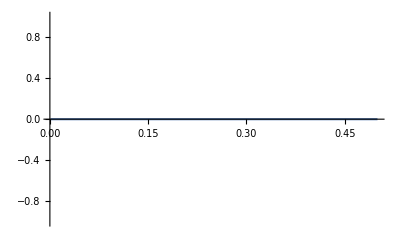

```mathematica
Plot[nxtxz[ig,ig,kkv,ig,ig,1.0,0.01][[4,1]],{kkv,0.001,.5}]
```

## Initialization

```mathematica
SetOptions[InputNotebook[],PrivateNotebookOptions->{"FileOutlineCache"->False},TrackCellChangeTimes->False](*use Cell->Delete All Output*)
Switch[$System,
"Mac OS X x86 (64-bit)",SetDirectory["/Users/garyanderson/git/ProjectionMethodTools/ProjectionMethodToolsJava/code"],
"Linux x86 (64-bit)",SetDirectory["~/git/ProjectionMethodTools/ProjectisteponMethodToolsJava/code"],
"Microsoft Windows (64-bit)",SetDirectory["g:/git/ProjectionMethodTools/ProjectionMethodToolsJava/code"]];
PrependTo[$Path,"../../../AMASeriesRepresentation/AMASeriesRepresentation/"];
Get["genArbLin.mth"]
Needs["simpleRBCModel`"]
Needs["betterRBC`"]Needs["betterQuasiRBC`"];Needs["betterCnstrnRBC`"]
```

using version in eclipse